# Useful Properties to query

To see information about the tables see: https://simbad.u-strasbg.fr/simbad/tap/tapsearch.html

Following I select what properties are useful for my function studying the tables as groups (groups are tables with the same color in the above link)

To report errors (in quantities) I followed Jose suggestion where each property have a “WithUncertainty” counterpart.

## Basic data

### From Identifiers group

• ids.ids: this pipe separated string must be converted to a list after the import.

### From Object types group

• There is not a direct column to return. Instead I am going to find all object type and return the description of the types as a list. Also, the code of the type could be returned.

### From basic table

• main_id

• Object type: this if the main object type. I can return the code and explanation.

#### Position parameters

• Right Ascension: this must include the unit and error. So this is an Around of a Quantity object.

• Declination: this must include the unit and error. So this is an Around of a Quantity object.

• Position Error ellipse.

• Position wavelength class.

• Position quality.

• Position reference. (?)

#### Proper motion parameters

•  Proper motion in right ascension: this must include the unit and error. So this is an Around of a Quantity object.

• Proper motion in declination: this must include the unit and error. So this is an Around of a Quantity object.

• Proper motion error ellipse.

• Proper motion quality.

• Proper motion reference. (?)

#### Parallax parameters

• Parallax with error as an Around[Quantity.

• Parallax quality.

• Parallax reference. (?)

#### Radial velocity parameters

Simbad has 3 ways to report radial velocities (radial velocity, redshift, and c times redshift). Simbad TAP tables repot only one of these for each astronomical object. Simbad web service reports the three ways for each object, I think that 2 of this ways are computed from the one given.

I can know the type of velocity from the rvz_type column, so that I will know if for a given object I have radial velocity, redshift, or cz.

• Radial velocity with error as Around[Quantity

• Redshift with error as Around[

• Quality of the reported velocity.

• Nature of the measurement of the velocity. (See the description of rvz_nature in http://simbad.u-strasbg.fr/simbad/sim-display?data=meas)

• Velocity reference (?)

There is another type of velocity “velocity in Local Standard of Rest reference frame”

• velocity in Local Standard of Rest reference frame (from vlsr)

#### Spectral type parameter

For spectral type and morphological type, I could make an algorithm to convert the codes of classification to more “usual” words.

• the type of the spectral type as an string. (Jeff does the same)

• Quality of the spectral type.

• Spectral type reference reference (?)

#### Morphological type

• The morphological type of a galaxy as a string.

• Quality of the morphological type.

• Morphological type reference (?)

#### Size of a galaxy

Here I follow what wolfram entities of galaxies do.

• Major axis as a Quantity

• Minor axis as a Quantity.

• Angle of the ellipse as a Quantity.

• Quality.

• Reference.

#### Update data??

### Flux data

The following data must include to these filters: U, B, V, R, I, J, H, K, u, g, r, i, z, G. There are 14 filters in total.

• Flux value as a Around[

• Flux quality.

• Flux reference.

## Measurement Types

All the following data can be not unique for a given astronomical object. There could be several observations and measurements of a certain property of an object. The table “basic” chooses only one of these properties, for example “basic” just report one parallax, but the mesPLX table reports several parallaxes for some objects. 
This data is not as organized as basic data.

### Velocities data

The data of this table already appears in the basic table.

In this table there are 7 409 800 rows.

### Spectral type data

The data of this table already appears in the basic table.

In this table there are 1 082 979 rows.

### Parallax data

The data of this table already appears in the basic table.

In this table there are 7 167 765 rows.

### Proper Motion data

The data of this table already appears in the basic table.

In this table there are 6 294 057 rows.

### Distance data

In this table there are 4 106 298 rows.

• Distance to the object as an Around[Quantity[

• Quality.

• Reference.

### Stellar parameters (Teff, log(g) and [Fe/H])

In this table there are 1 035 930 rows.

• Effective temperature as Quantity[  (in K)

• Decimal logarithm of the surface gravity as Quantity[ (in m/s^2)

• Metallicity index relative to the Sun. (This can be problematic because sometimes the sun is not the comparison star.)

• Reference.

### Variable Stars data

In this table there are 1 806 908 rows.

• Maximum bright.

• Minimum bright.

• Period as Quantity[

• Epoch in Julian days.

• Type of variability.

• Magnitude type. (?)

• Reference. (?)

### Diameter of stars data

In this table there are 6 690 rows.

• diameter of the star as an Around[Quantity[

• Quality.

• Reference.

### Rotational parameters

In this table there are 75 691

• Projected rotational velocity (vsini) as an Around[Quantity[

• Quality.

• Reference.

# Trying different mirrors if Simbad

There is only one mirror of SIMBAD owned by Harvard.

```mathematica
rootHarvard="http://simbad.cfa.harvard.edu/simbad/sim-tap/sync?request=doQuery&lang=adql&format=tsv&query=";
```

It seems to work

# Testing sky regions

This is how to specify a region in AstroData function. In the following parameters, if an argument is a number it is assumed to be in degrees.

```mathematica
(* This is a circle *)
AstroData[<|AstroCenter->{ra,dec},AstroRange->x,MaxItems->x|>,prop]
```

```mathematica
(* This is a rectangle *)
AstroData[<|AstroRange->{{ra1,ra2},{dec1,dec2}},MaxItems->x|>,prop]
```

```mathematica
(* This is a polygon. Where the value of Astrorange has at least three vertexes. *)
AstroData[<|AstroRange->{{ra1,dec1},{ra2,dec2},...},MaxItems->x|>,prop]
```

```mathematica
(* This is a search by objects *)
AstroData[<|"Objects"->{"obj1","obj2",...}|>,prop]
AstroData[<|"Objects"->"obj"|>,prop]
```

### Circle

In ADQL the circle function is: CIRCLE(coord_sys, ra_center, dec_center, radius_in_degree)

The radius must be in the range 90°>r>0°.

Circle is going to be specified by a center and a radius.

• The center is specified as:

```mathematica
AstroCenter->{ra,dec}
```

• The radius is specified as:

```mathematica
AstroRange->r
```

#### Errors in the function

• The declination of the center of the circle must be in the interval -90°≤dec≤90° to get expected results.

• And the radius must be 90°>r>0°.

### Box

The box function of Simbad keeps the ra and dec constant .

The box function of Simbad is: BOX(coord_sys, ra_center, dec_center, width_in_degrees, height_in_degrees), there is no limit in the width and height of the box. The box function seems to break when the height is larger than 180.

• Some estrange behavior happens in this function, for example when the height of a box in Simbad that exceeds the declination limit of 90°:

```mathematica
query=URLEncode@"SELECT TOP 3000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), BOX('ICRS', 0,45,360,90)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

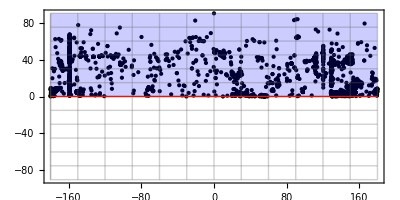

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],Blue,Polygon[GeoPosition[Reverse[{{-180,0},{180,0},{180,90},{-180,90}},{2}]]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->True,GeoRange->All,GeoCenter->Automatic,GeoProjection->None,GeoBackground->None]
```

• A box is going to be specified as:

```mathematica
AstroRange->{{ra1,ra2},{dec1,dec2}}
```

#### Errors in the function

• The declination in the edges of the rectangle can not exceed the limits.

### Polygon

In Simbad the POLYGON function is: POLYGON(coord_sys, ra_vertice1, dec_vertice1, ra_vertice2, dec_vertice2, ra_vertice3, dec_vertice3 [, ...]).

This function connects each vertex with the next one following a geodesic.

This functions requires at least 3 vertices, but the three vertices could be in the same line (GeoPolygon can’t).

GeoPolygon supports things like GeoPolygon[GeoPosition[Reverse[{{0,85},{30,85},{180,89},{15,80}},{2}]]] (where segments of the polygon cross), but Simbad POLYGON can’t.

The polygon in the sky is going to be specified in AstroData as:

```mathematica
AstroRange->{{ra1,dec1},{ra2,dec2},{ra3,dec3},...}
```

#### Errors in the function

• The dec of the vertexes must be in the correct range to not getting unexpected positions.

• This function works well as long as it receives at least 3 different vertexes (although the vertexes can lie in the same line).

• The resulting polygon cannot have crossing segments (i.e. GeoPolygon[GeoPosition[Reverse[{{0,85},{30,85},{180,89},{15,80}},{2}]]]).

• A segment in the polygon can not be 180°.

```mathematica
query=URLEncode@"SELECT TOP 3000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), POLYGON('ICRS', -720,0,-720,20,1981,20,1981,0)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

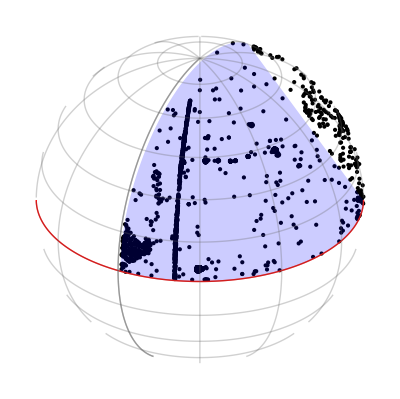

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],Blue,GeoPolygon[GeoPosition[Reverse[{{0,0},{0,20},{181,20},{181,0}},{2}]]](*,Blue,Polygon[GeoPosition[Reverse[{{0,85},{30,85},{180,89}},{2}]]]*),Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoCenter->Automatic,GeoProjection->{"Orthographic","Centering"->{30,-150}},GeoBackground->None,GeoRange->"World"]
```

### Drafts testing the sky functions of Simbad

#### Testing a vertex out of range in the declination in POLYGON function

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), POLYGON('ICRS', 0,0,90,0,0,181)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

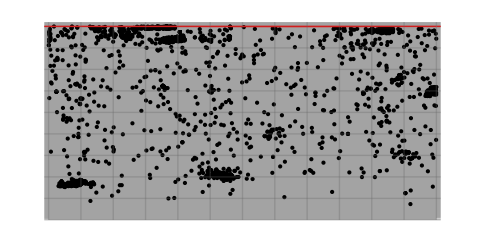

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],Black,GeoPolygon[GeoPosition[Reverse[{{0,0},{90,0},{180,-1}},{2}]]],Blue,Red,GeoPath["Equator"],Polygon[GeoPosition[Reverse[{{0,0},{90,0},{180,-1}},{2}]]]},GeoGridLines->Automatic,Frame->False,GeoProjection->None,GeoBackground->None,GeoRange->{{2,-90},{-2,182}}]
```

In conclusion, the vertex (0, 181) just is converted to the vertex (180, -1), which is logic but estrange.

#### This is what happen when one of the vertices in a polygon in not in the correct limits of declination.

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), POLYGON('ICRS', 0,85,30,85,0,91)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

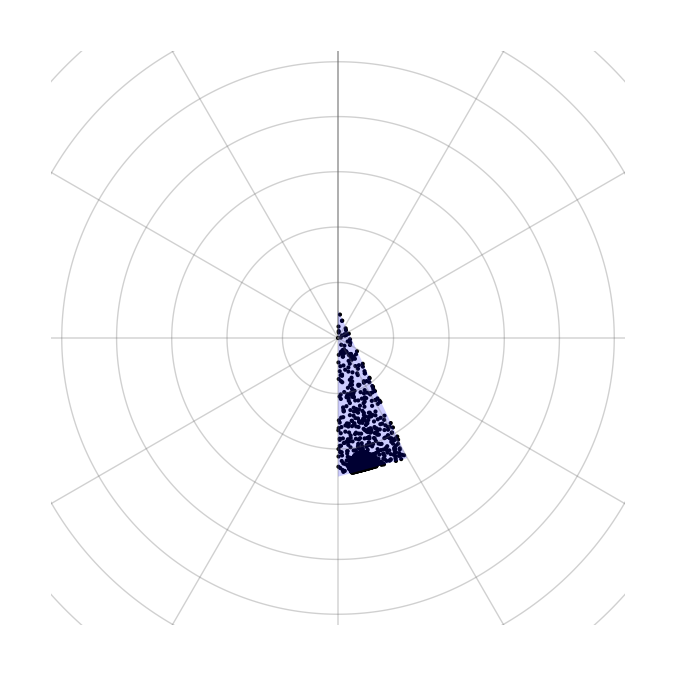

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],Blue,GeoPolygon[GeoPosition[Reverse[{{0,85},{30,85},{180,89}},{2}]]](*,Blue,Polygon[GeoPosition[Reverse[{{0,85},{30,85},{180,89}},{2}]]]*),Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoCenter->Automatic,GeoProjection->{"Orthographic","Centering"->{90,0}},GeoBackground->None,GeoRange->{{80., 90.}, {-180., 180.}}]
```

In this case the vertex (0, 91) is translated to (180,89).

#### • POLYGON join the vertices with geodesics.

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), POLYGON('ICRS', -80,-50,-80,-20,0,0,80,-20,80,-50)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

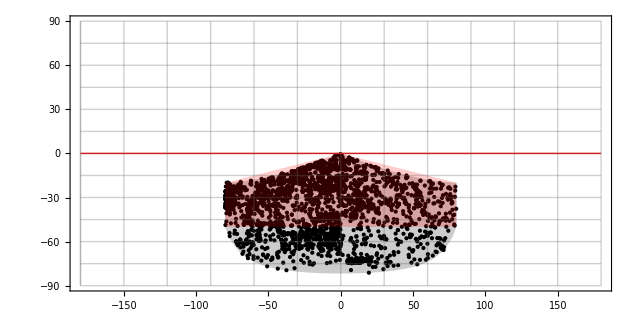

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoPolygon[Reverse[{{-80,-50},{-80,-20},{0,0},{80,-20},{80,-50}},{2}]],Red,Polygon[GeoPosition[Reverse[{{-80,-50},{-80,-20},{0,0},{80,-20},{80,-50}},{2}]]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->True,GeoRange->All,GeoCenter->Automatic,GeoProjection->"Equirectangular",GeoBackground->None]
```

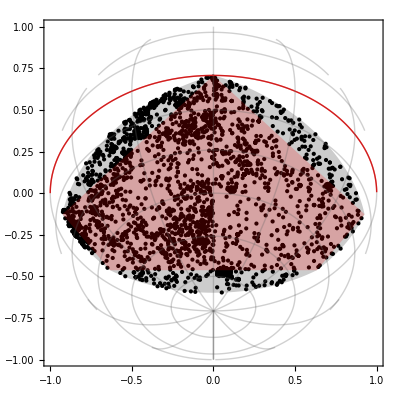

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoPolygon[GeoPosition[Reverse[{{-80,-50},{-80,-20},{0,0},{80,-20},{80,-50}},{2}]]],Red,Polygon[GeoPosition[Reverse[{{-80,-50},{-80,-20},{0,0},{80,-20},{80,-50}},{2}]]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->True,GeoRange->All,GeoCenter->Automatic,GeoProjection->{"Orthographic","Centering"->{-45,0}},GeoBackground->None]
```

#### • The box region in Simbad does not join the vertices with geodesics.

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), BOX('ICRS', 45, -45, 120, 10)) = 1;";
AbsoluteTiming[result=Import[root~~query];]
points=Rest@result[[All,{3,4}]];
```

{1.97169,Null}

```mathematica
Length[result]
```

5001

```mathematica
ByteCount[result]
```

873320

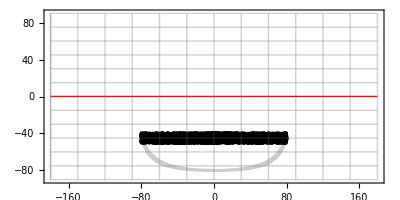

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoPolygon[Reverse[{{-80,-40},{-80,-50},{80,-50},{80,-40}},{2}]],Polygon[{{-80,-40},{-80,-50},{80,-50},{80,-40}}],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->True,GeoRange->All,GeoCenter->Automatic,GeoProjection->"Equirectangular",GeoBackground->None]
```

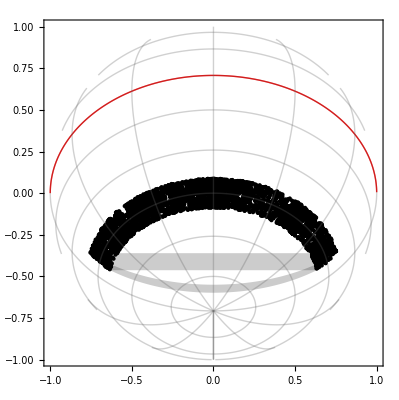

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoPolygon[Reverse[{{-80,-40},{-80,-50},{80,-50},{80,-40}},{2}]],Polygon[GeoPosition[Reverse[{{-80,-40},{-80,-50},{80,-50},{80,-40}},{2}]]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->True,GeoRange->All,GeoCenter->Automatic,GeoProjection->{"Orthographic","Centering"->{-45,0}},GeoBackground->None]
```

#### Notes about how Simbad deals with sky regions

• A position in the sky is specified in the range 360°>ra>0° and 90°>de>-90°. But any angle (positive or negative) can be given as argument. Simbad seems to work wrong estrange when the declination is not in the right limits. Right Ascension can be given as a negative angle, and mod 360 is calculated.

• There are 3 functions to specify a region in Simbad circle, box, and polygon.

• The circle is specified by a center and a radius. The radius must be in the range 90°>r>0°.

This function seems to work well when the angles are in the correct range:

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), CIRCLE('ICRS', 10, 10, 10)) = 1";
result=Import[rootHarvard~~query];
points=Rest@result[[All,{3,4}]];
```

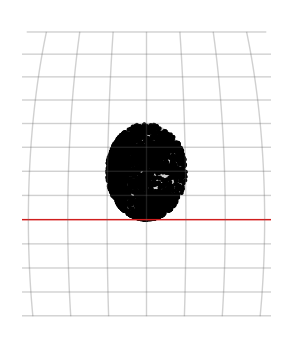

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoDisk[{10,10},Quantity[10,"AngularDegrees"]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoRange->Quantity[30,"AngularDegrees"],GeoCenter->GeoPosition[{10,10}],GeoProjection->"Mollweide",GeoBackground->None]
```

But fails when the declination angle is not in the correct range:

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), CIRCLE('ICRS',180, 100, 10)) = 1";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

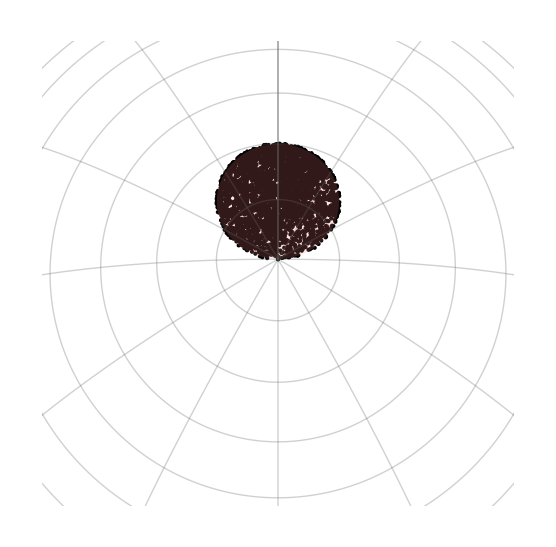

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],Pink,GeoDisk[{80,0},Quantity[10,"AngularDegrees"]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoRange->Quantity[30,"AngularDegrees"],GeoCenter->GeoPosition[{80,180}],GeoProjection->"Orthographic",GeoBackground->None]
```

• Box seems to work wrong when the center of the box is not in the proper range of the celestial sphere as the circle.

This is a good range:

```mathematica
query=URLEncode@"SELECT TOP 500 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), BOX('ICRS', 270, -45, 5, 5)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

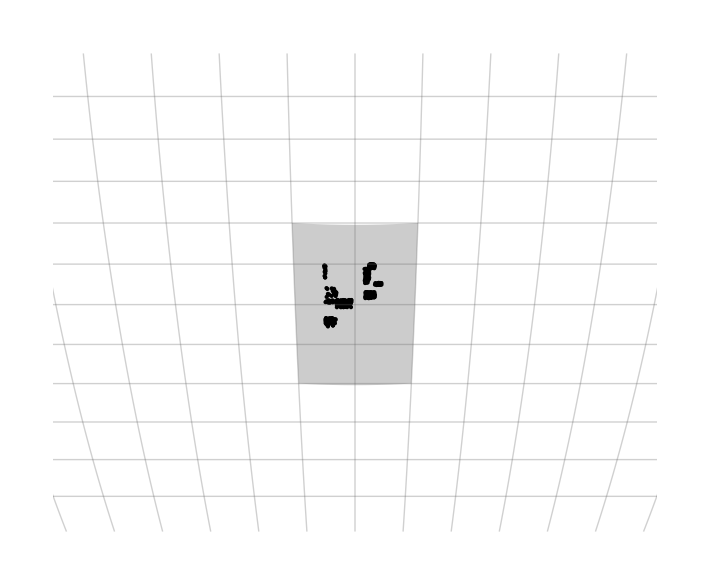

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoPolygon[{{-50,275},{-50,265},{-40,265},{-40,275}}],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoRange->Quantity[15,"AngularDegrees"],GeoCenter->GeoPosition[{-45,270}],GeoProjection->"Mollweide",GeoBackground->None]
```

This example is a bad range:

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), BOX('ICRS', 10, -100, 10, 10)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

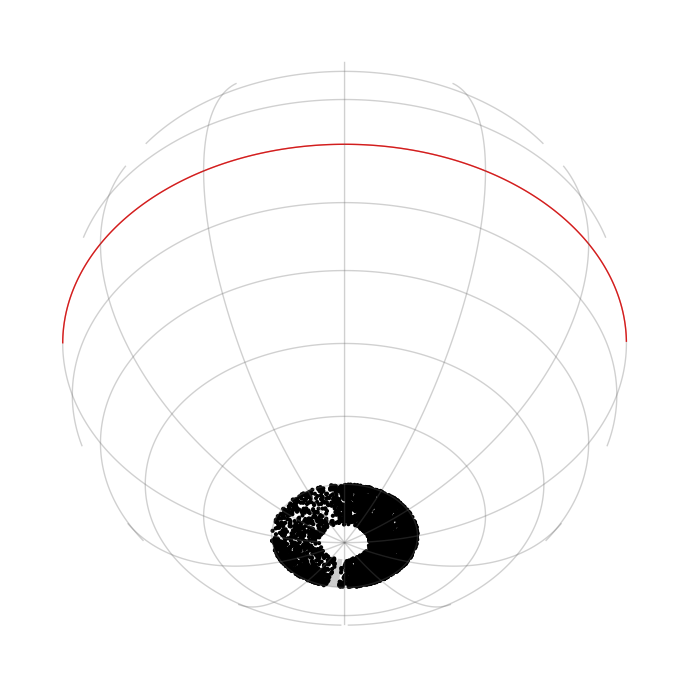

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],Polygon[GeoPosition[Reverse[{{180+5,-85},{180+5,-75},{180+15,-75},{180+15,-85}},{2}]]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoRange->"World",GeoCenter->GeoPosition[{-80,10}],GeoProjection->{"Orthographic","Centering"->{-45,0}},GeoBackground->None]
```

• Polygon

```mathematica
query=URLEncode@"SELECT TOP 5000 oid, main_id, ra, dec
FROM basic WHERE CONTAINS(POINT('ICRS', ra, dec), POLYGON('ICRS', 10,-50.6,70,0.2,20,30,-30,0,0,0)) = 1;";
result=Import[root~~query];
points=Rest@result[[All,{3,4}]];
```

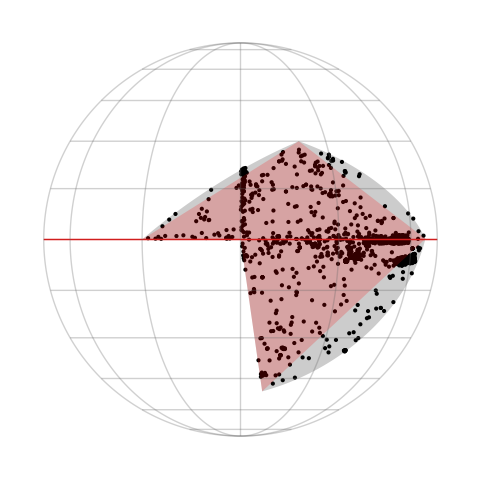

```mathematica
GeoGraphics[{Point[GeoPosition[Reverse[points,2]]],GeoPolygon[GeoPosition[Reverse[{{10,-50.6},{70,0.2},{20,30},{-30,0},{0,0}},{2}]]],Red,Polygon[GeoPosition[Reverse[{{10,-50.6},{70,0.2},{20,30},{-30,0},{0,0}},{2}]]],Red,GeoPath["Equator"]},GeoGridLines->Automatic,Frame->False,GeoRange->"World",GeoCenter->Automatic,GeoProjection->"Orthographic",GeoBackground->None]
```

• Because the sky functions of Simbad does not work properly out of the range, I am going to return a error message if the range in the sky is not respected.

# Information of the properties of AstroData

The following info is what I use to know what columns and tables I have to query from Simbad to construct a given Property.

```mathematica
infoProperties={<|"Property Name"->"Identifiers","Description"->"List of all the identifiers of an astronomical object","Head"->List,"Example"->{"Nenque","HD 6434","..."},"Units"->None,"Simbad Columns Called"->{"ids.ids"},"Comment"->"","Simbad Tables Involved"->{"ids"},"Simbad Columns Returned"->{"ids"}|>,
<|"Property Name"->"MainIdentifier","Description"->"Main identifier used by Simbad","Head"->String,"Example"->"HD 6434","Units"->None,"Simbad Columns Called"->{"basic.main_id"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"main_id"}|>,
<|"Property Name"->"ObjectTypes","Description"->"List of the object types that the astronomical object is","Head"->List,"Example"->{"transient event","Radio-source","..."},"Units"->None,"Simbad Columns Called"->{"alltypes.otypes"},"Comment"->"","Simbad Tables Involved"->{"alltypes"},"Simbad Columns Returned"->{"otypes"}|>,<|"Property Name"->"MainObjectType","Description"->"Main object type","Head"->String,"Example"->"Star","Units"->None,"Simbad Columns Called"->{"basic.otype_txt"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"otype_txt"}|>,<|"Property Name"->"RightAscensionWithUncertainty","Description"->"Right Ascension with uncertainty","Head"->Quantity[Around],"Example"->Quantity[(1.000.10), "AngularDegrees"],"Units"->Quantity[1, "AngularDegrees"],"Simbad Columns Called"->{"basic.ra","basic.dec","basic.coo_err_maj","basic.coo_err_min","basic.coo_err_angle"},"Comment"->"This must be transformed from the ellipse error of Simbad.\nOnly if the error is available the property will exist.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"ra","dec","coo_err_maj","coo_err_min","coo_err_angle"}|>,<|"Property Name"->"RightAscension","Description"->"Right Ascension","Head"->Quantity,"Example"->Quantity[30, "AngularDegrees"],"Units"->Quantity[1, "AngularDegrees"],"Simbad Columns Called"->{"basic.ra"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"ra"}|>,<|"Property Name"->"DeclinationWithUncertainty","Description"->"Declination with uncertainty","Head"->Quantity[Around],"Example"->Quantity[(1.000.10), "AngularDegrees"],"Units"->Quantity[1, "AngularDegrees"],"Simbad Columns Called"->{"basic.dec","basic.ra","basic.coo_err_maj","basic.coo_err_min","basic.coo_err_angle"},"Comment"->"This must be transformed from the ellipse error of Simbad.\nOnly if the error is available the property will exist.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"dec","ra","coo_err_maj","coo_err_min","coo_err_angle"}|>,<|"Property Name"->"Declination","Description"->"Declination","Head"->Quantity,"Example"->Quantity[30, "AngularDegrees"],"Units"->Quantity[1, "AngularDegrees"],"Simbad Columns Called"->{"basic.dec"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"dec"}|>,<|"Property Name"->"PositionErrorEllipse","Description"->"Error in position shown as error ellipse","Head"->VectorAround,"Example"->VectorAround[{1.0778195484261666,-0.5117817865411112},{{0.004098748158802123,0.01886916685785904},{0.01886916685785904,0.10778396789058062}}],"Units"->Quantity[1, "AngularDegrees"],"Simbad Columns Called"->{"basic.dec","basic.ra","basic.coo_err_maj","basic.coo_err_min","basic.coo_err_angle"},"Comment"->"This must be transformed from the ellipse error of Simbad.\nThis will exists only if there is error.\nI should check how to return the units.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"dec","ra","coo_err_maj","coo_err_min","coo_err_angle"}|>,<|"Property Name"->"PositionWavelengthClass","Description"->"Wavelength class for the origin of the coordinates ","Head"->String,"Example"->"IR","Units"->None,"Simbad Columns Called"->{"basic.coo_wavelength"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"coo_wavelength"}|>,<|"Property Name"->"PositionQuality","Description"->"Quality of the position.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.coo_qual"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"coo_qual"}|>,<|"Property Name"->"PositionBibcode","Description"->"Bibcode of the position.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.coo_bibcode"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"coo_bibcode"}|>,<|"Property Name"->"ProperMotionRightAscensionWithUncertainty","Description"->"Proper motion in right ascension with uncertainty.","Head"->Quantity[Around],"Example"->Quantity[(1.000.10), ("MilliarcSeconds")/("Years")],"Units"->Quantity[1, ("MilliarcSeconds")/("Years")],"Simbad Columns Called"->{"basic.pmra","basic.pm_err_maj","basic.pm_err_min","basic.pm_err_angle"},"Comment"->"This must be transformed from the ellipse error of Simbad.\nOnly if the error is available the property will exist.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pmra","pm_err_maj","pm_err_min","pm_err_angle"}|>,<|"Property Name"->"ProperMotionRightAscension","Description"->"Proper motion in right ascension.","Head"->Quantity,"Example"->Quantity[5, ("MilliarcSeconds")/("Years")],"Units"->Quantity[1, ("MilliarcSeconds")/("Years")],"Simbad Columns Called"->{"basic.pmra"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pmra"}|>,<|"Property Name"->"ProperMotionDeclinationWithUncertainty","Description"->"Proper motion in declination with uncertainty.","Head"->Quantity[Around],"Example"->Quantity[(1.000.10), ("MilliarcSeconds")/("Years")],"Units"->Quantity[1, ("MilliarcSeconds")/("Years")],"Simbad Columns Called"->{"basic.pmdec","basic.pm_err_maj","basic.pm_err_min","basic.pm_err_angle"},"Comment"->"This must be transformed from the ellipse error of Simbad.\nOnly if the error is available the property will exist.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pmdec","pm_err_maj","pm_err_min","pm_err_angle"}|>,<|"Property Name"->"ProperMotionDeclination","Description"->"Proper motion in declination.","Head"->Quantity,"Example"->Quantity[5, ("MilliarcSeconds")/("Years")],"Units"->Quantity[1, ("MilliarcSeconds")/("Years")],"Simbad Columns Called"->{"basic.pmdec"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pmdec"}|>,<|"Property Name"->"ProperMotionErrorEllipse","Description"->"Error in proper motion shown as error ellipse","Head"->VectorAround,"Example"->VectorAround[{1.0778195484261666,-0.5117817865411112},{{0.004098748158802123,0.01886916685785904},{0.01886916685785904,0.10778396789058062}}],"Units"->Quantity[1, degree per year],"Simbad Columns Called"->{"basic.pmra","basic.pmdec","basic.pm_err_maj","basic.pm_err_min","basic.pm_err_angle"},"Comment"->"This must be transformed from the ellipse error of Simbad.\nThis will exists only if there is error.\nI should check how to return the units.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pmra","pmdec","pm_err_maj","pm_err_min","pm_err_angle"}|>,<|"Property Name"->"ProperMotionQuality","Description"->"Quality of the proper motion.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.pm_qual"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pm_qual"}|>,<|"Property Name"->"ProperMotionBibcode","Description"->"Bibcode of the proper motion.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.pm_bibcode"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"pm_bibcode"}|>,<|"Property Name"->"ParallaxWithUncertainty","Description"->"Parallax with uncertainty","Head"->Quantity[Around],"Example"->Quantity[(1.000.10), "MilliarcSeconds"],"Units"->Quantity[1, "MilliarcSeconds"],"Simbad Columns Called"->{"basic.plx_value","basic.plx_err"},"Comment"->"Only if the error is available the property exist.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"plx_value","plx_err"}|>,<|"Property Name"->"Parallax","Description"->"Parallax","Head"->Quantity,"Example"->Quantity[10, "MilliarcSeconds"],"Units"->Quantity[1, "MilliarcSeconds"],"Simbad Columns Called"->{"basic.plx_value"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"plx_value"}|>,<|"Property Name"->"ParallaxQuality","Description"->"Quality of the parallax.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.plx_qual"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"plx_qual"}|>,<|"Property Name"->"ParallaxBibcode","Description"->"Bibcode of the parallax.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.plx_bibcode"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"plx_bibcode"}|>,<|"Property Name"->"RedshiftWithUncertainty","Description"->"Redshift with uncertainty","Head"->Around,"Example"->1.000.10,"Units"->None,"Simbad Columns Called"->{"basic.rvz_type","basic.rvz_redshift","basic.rvz_err"},"Comment"->"Redshift of obejects in Simbad come from measurement or from computation from radial velocity. Computed redshifts are not good at large redshift because Simbad uses special relativistic formula of redshift, for example see the redsift of the object \"[ORN2011] 003.584125-30.483750\" the velocity in this case should be larger than c. I propese making my own computations of redshift or returning just the mesurement not the computation. One knows if the value is measurement or computation seeing the column basic.rvz_type","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_type","rvz_redshift","rvz_err"}|>,<|"Property Name"->"Redshift","Description"->"Redshift","Head"->Real,"Example"->1.,"Units"->None,"Simbad Columns Called"->{"basic.rvz_type","basic.rvz_redshift"},"Comment"->"Same comment as RedshiftWithUncertainty.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_type","rvz_redshift"}|>,
<|"Property Name"->"RedshiftQuality","Description"->"Quality of the redshift.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.rvz_qual","basic.rvz_type"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_qual","rvz_type"}|>,<|"Property Name"->"RedshiftBibcode","Description"->"Bibcode of the redshift.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.rvz_bibcode","basic.rvz_type"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_bibcode","rvz_type"}|>,<|"Property Name"->"RadialVelocityWithUncertainty","Description"->"Radial velocity with uncertainty.","Head"->Quantity[Around],"Example"->Quantity[(1.000.10), ("Kilometers")/("Seconds")],"Units"->Quantity[1, ("Kilometers")/("Seconds")],"Simbad Columns Called"->{"basic.rvz_type","basic.rvz_radvel","basic.rvz_err"},"Comment"->"Radial velocity has the same problem as redshift.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_type","rvz_radvel","rvz_err"}|>,<|"Property Name"->"RadialVelocity","Description"->"Radial velocity.","Head"->Quantity,"Example"->Quantity[10, ("Kilometers")/("Seconds")],"Units"->Quantity[1, ("Kilometers")/("Seconds")],"Simbad Columns Called"->{"basic.rvz_type","basic.rvz_radvel"},"Comment"->"Radial velocity has the same problem as redshift.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_type","rvz_radvel"}|>,<|"Property Name"->"RadialVelocityQuality","Description"->"Quality of the radial velocity.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.rvz_qual","basic.rvz_type"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_qual","rvz_type"}|>,<|"Property Name"->"RadialVelocityBibcode","Description"->"Bibcode of the radial velocity.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.rvz_bibcode","basic.rvz_type"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"rvz_bibcode","rvz_type"}|>,
<|"Property Name"->"SpectralClass","Description"->"Code of spectral classification","Head"->String,"Example"->"G2V","Units"->None,"Simbad Columns Called"->{"basic.sp_type"},"Comment"->"I could add properties that extract info from the code.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"sp_type"}|>,<|"Property Name"->"SpectralClassQuality","Description"->"Quality of the spectral class.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.sp_qual"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"sp_qual"}|>,<|"Property Name"->"SpectralClassBibcode","Description"->"Bibcode of the spectral class.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.sp_bibcode"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"sp_bibcode"}|>,<|"Property Name"->"MorphologicalClass","Description"->"Code of morphological classification","Head"->String,"Example"->"(R')SB(s)0/a","Units"->None,"Simbad Columns Called"->{"basic.morph_type"},"Comment"->"I could add properties that extract info from the code.","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"morph_type"}|>,<|"Property Name"->"MorphologicalClassQuality","Description"->"Quality of the morphological class.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.morph_qual"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"morph_qual"}|>,<|"Property Name"->"MorphologicalClassBibcode","Description"->"Bibcode of the morphological class.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.morph_bibcode"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"morph_bibcode"}|>,<|"Property Name"->"GalaxyMajorAxis","Description"->"Angular size major axis","Head"->Quantity,"Example"->Quantity[0.5, "ArcMinutes"],"Units"->Quantity[1, "ArcMinutes"],"Simbad Columns Called"->{"basic.galdim_majaxis"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"galdim_majaxis"}|>,<|"Property Name"->"GalaxyMinorAxis","Description"->"Angular size minor axis","Head"->Quantity,"Example"->Quantity[0.5, "ArcMinutes"],"Units"->Quantity[1, "ArcMinutes"],"Simbad Columns Called"->{"basic.galdim_minaxis"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"galdim_minaxis"}|>,<|"Property Name"->"GalaxyPositionAngle","Description"->"Galaxy ellipse angle","Head"->Quantity,"Example"->Quantity[45, "AngularDegrees"],"Units"->Quantity[1, "AngularDegrees"],"Simbad Columns Called"->{"basic.galdim_angle"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"galdim_angle"}|>,<|"Property Name"->"GalaxySizeQuality","Description"->"Quality of the galaxy size.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"basic.galdim_qual"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"galdim_qual"}|>,<|"Property Name"->"GalaxySizeBibcode","Description"->"Bibcode of the galaxy size.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"basic.galdim_bibcode"},"Comment"->"","Simbad Tables Involved"->{"basic"},"Simbad Columns Returned"->{"galdim_bibcode"}|>,<|"Property Name"->"VMagnitudeWithUncertainty","Description"->"Magnitude in the filter V.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"v.flux as \"V\"","v.flux_err as \"V_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux v"},"Simbad Columns Returned"->{"V","V_err"}|>,<|"Property Name"->"VMagnitude","Description"->"Magnitude in the filter V.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"v.flux as \"V\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux v"},"Simbad Columns Returned"->{"V"}|>,<|"Property Name"->"VMagnitudeQuality","Description"->"Quality of the magnitude in the V filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"v.qual as \"V_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux v"},"Simbad Columns Returned"->{"V_qual"}|>,<|"Property Name"->"VMagnitudeBibcode","Description"->"Bibcode of the magnitude in the V filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"v.bibcode as \"V_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux v"},"Simbad Columns Returned"->{"V_bib"}|>,(* --U-- *)
<|"Property Name"->"UMagnitudeWithUncertainty","Description"->"Magnitude in the filter U.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"u.flux as \"U\"","u.flux_err as \"U_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux u"},"Simbad Columns Returned"->{"U","U_err"}|>,<|"Property Name"->"UMagnitude","Description"->"Magnitude in the filter U.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"u.flux as \"U\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux u"},"Simbad Columns Returned"->{"U"}|>,<|"Property Name"->"UMagnitudeQuality","Description"->"Quality of the magnitude in the U filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"u.qual as \"U_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux u"},"Simbad Columns Returned"->{"U_qual"}|>,<|"Property Name"->"UMagnitudeBibcode","Description"->"Bibcode of the magnitude in the U filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"u.bibcode as \"U_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux u"},"Simbad Columns Returned"->{"U_bib"}|>,
(* --B-- *)
<|"Property Name"->"BMagnitudeWithUncertainty","Description"->"Magnitude in the filter B.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"b.flux as \"B\"","b.flux_err as \"B_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux b"},"Simbad Columns Returned"->{"B","B_err"}|>,<|"Property Name"->"BMagnitude","Description"->"Magnitude in the filter B.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"b.flux as \"B\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux b"},"Simbad Columns Returned"->{"B"}|>,<|"Property Name"->"BMagnitudeQuality","Description"->"Quality of the magnitude in the B filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"b.qual as \"B_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux b"},"Simbad Columns Returned"->{"B_qual"}|>,<|"Property Name"->"BMagnitudeBibcode","Description"->"Bibcode of the magnitude in the B filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"b.bibcode as \"B_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux b"},"Simbad Columns Returned"->{"B_bib"}|>,
(* --R-- *)
<|"Property Name"->"RMagnitudeWithUncertainty","Description"->"Magnitude in the filter R.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"r.flux as \"R\"","r.flux_err as \"R_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux r"},"Simbad Columns Returned"->{"R","R_err"}|>,<|"Property Name"->"RMagnitude","Description"->"Magnitude in the filter R.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"r.flux as \"R\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux r"},"Simbad Columns Returned"->{"R"}|>,<|"Property Name"->"RMagnitudeQuality","Description"->"Quality of the magnitude in the R filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"r.qual as \"R_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux r"},"Simbad Columns Returned"->{"R_qual"}|>,<|"Property Name"->"RMagnitudeBibcode","Description"->"Bibcode of the magnitude in the R filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"r.bibcode as \"R_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux r"},"Simbad Columns Returned"->{"R_bib"}|>,
(* --I-- *)
<|"Property Name"->"IMagnitudeWithUncertainty","Description"->"Magnitude in the filter I.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"i.flux as \"I\"","i.flux_err as \"I_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux i"},"Simbad Columns Returned"->{"I","I_err"}|>,<|"Property Name"->"IMagnitude","Description"->"Magnitude in the filter I.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"i.flux as \"I\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux i"},"Simbad Columns Returned"->{"I"}|>,<|"Property Name"->"IMagnitudeQuality","Description"->"Quality of the magnitude in the I filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"i.qual as \"I_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux i"},"Simbad Columns Returned"->{"I_qual"}|>,<|"Property Name"->"IMagnitudeBibcode","Description"->"Bibcode of the magnitude in the I filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"i.bibcode as \"I_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux i"},"Simbad Columns Returned"->{"I_bib"}|>,
(* --J--*)
<|"Property Name"->"JMagnitudeWithUncertainty","Description"->"Magnitude in the filter J.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"j.flux as \"J\"","j.flux_err as \"J_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux j"},"Simbad Columns Returned"->{"J","J_err"}|>,<|"Property Name"->"JMagnitude","Description"->"Magnitude in the filter J.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"j.flux as \"J\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux j"},"Simbad Columns Returned"->{"J"}|>,<|"Property Name"->"JMagnitudeQuality","Description"->"Quality of the magnitude in the J filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"j.qual as \"J_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux j"},"Simbad Columns Returned"->{"J_qual"}|>,<|"Property Name"->"JMagnitudeBibcode","Description"->"Bibcode of the magnitude in the J filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"j.bibcode as \"J_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux j"},"Simbad Columns Returned"->{"J_bib"}|>,
(* --H-- *)
<|"Property Name"->"HMagnitudeWithUncertainty","Description"->"Magnitude in the filter H.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"h.flux as \"H\"","h.flux_err as \"H_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux h"},"Simbad Columns Returned"->{"H","H_err"}|>,<|"Property Name"->"HMagnitude","Description"->"Magnitude in the filter H.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"h.flux as \"H\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux h"},"Simbad Columns Returned"->{"H"}|>,<|"Property Name"->"HMagnitudeQuality","Description"->"Quality of the magnitude in the H filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"h.qual as \"H_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux h"},"Simbad Columns Returned"->{"H_qual"}|>,<|"Property Name"->"HMagnitudeBibcode","Description"->"Bibcode of the magnitude in the H filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"h.bibcode as \"H_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux h"},"Simbad Columns Returned"->{"H_bib"}|>,
(* --K-- *)
<|"Property Name"->"KMagnitudeWithUncertainty","Description"->"Magnitude in the filter K.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"k.flux as \"K\"","k.flux_err as \"K_err\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux k"},"Simbad Columns Returned"->{"K","K_err"}|>,<|"Property Name"->"KMagnitude","Description"->"Magnitude in the filter K.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"k.flux as \"K\""},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux k"},"Simbad Columns Returned"->{"K"}|>,<|"Property Name"->"KMagnitudeQuality","Description"->"Quality of the magnitude in the K filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"k.qual as \"K_qual\""},"Comment"->"","Simbad Tables Involved"->{"flux k"},"Simbad Columns Returned"->{"K_qual"}|>,<|"Property Name"->"KMagnitudeBibcode","Description"->"Bibcode of the magnitude in the K filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"k.bibcode as \"K_bib\""},"Comment"->"","Simbad Tables Involved"->{"flux k"},"Simbad Columns Returned"->{"K_bib"}|>,
(* --u-- *)
<|"Property Name"->"SDSSUMagnitudeWithUncertainty","Description"->"Magnitude in the filter u.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"sdssu.flux as u","sdssu.flux_err as u_err"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssu"},"Simbad Columns Returned"->{"u","u_err"}|>,<|"Property Name"->"SDSSUMagnitude","Description"->"Magnitude in the filter u.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"sdssu.flux as u"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssu"},"Simbad Columns Returned"->{"u"}|>,<|"Property Name"->"SDSSUMagnitudeQuality","Description"->"Quality of the magnitude in the u filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"sdssu.qual as u_qual"},"Comment"->"","Simbad Tables Involved"->{"flux sdssu"},"Simbad Columns Returned"->{"u_qual"}|>,<|"Property Name"->"SDSSUMagnitudeBibcode","Description"->"Bibcode of the magnitude in the u filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"sdssu.bibcode as u_bib"},"Comment"->"","Simbad Tables Involved"->{"flux sdssu"},"Simbad Columns Returned"->{"u_bib"}|>,
(* --g-- *)
<|"Property Name"->"SDSSGMagnitudeWithUncertainty","Description"->"Magnitude in the filter g.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"sdssg.flux as g","sdssg.flux_err as g_err"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssg"},"Simbad Columns Returned"->{"g","g_err"}|>,<|"Property Name"->"SDSSGMagnitude","Description"->"Magnitude in the filter g.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"sdssg.flux as g"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssg"},"Simbad Columns Returned"->{"g"}|>,<|"Property Name"->"SDSSGMagnitudeQuality","Description"->"Quality of the magnitude in the g filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"sdssg.qual as g_qual"},"Comment"->"","Simbad Tables Involved"->{"flux sdssg"},"Simbad Columns Returned"->{"g_qual"}|>,<|"Property Name"->"SDSSGMagnitudeBibcode","Description"->"Bibcode of the magnitude in the g filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"sdssg.bibcode as g_bib"},"Comment"->"","Simbad Tables Involved"->{"flux sdssg"},"Simbad Columns Returned"->{"g_bib"}|>,
(* --r-- *)
<|"Property Name"->"SDSSRMagnitudeWithUncertainty","Description"->"Magnitude in the filter r.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"sdssr.flux as r","sdssr.flux_err as r_err"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssr"},"Simbad Columns Returned"->{"r","r_err"}|>,<|"Property Name"->"SDSSRMagnitude","Description"->"Magnitude in the filter r.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"sdssr.flux as r"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssr"},"Simbad Columns Returned"->{"r"}|>,<|"Property Name"->"SDSSRMagnitudeQuality","Description"->"Quality of the magnitude in the r filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"sdssr.qual as r_qual"},"Comment"->"","Simbad Tables Involved"->{"flux sdssr"},"Simbad Columns Returned"->{"r_qual"}|>,<|"Property Name"->"SDSSRMagnitudeBibcode","Description"->"Bibcode of the magnitude in the r filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"sdssr.bibcode as r_bib"},"Comment"->"","Simbad Tables Involved"->{"flux sdssr"},"Simbad Columns Returned"->{"r_bib"}|>,
(* --i-- *)
<|"Property Name"->"SDSSIMagnitudeWithUncertainty","Description"->"Magnitude in the filter i.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"sdssi.flux as i","sdssi.flux_err as i_err"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssi"},"Simbad Columns Returned"->{"i","i_err"}|>,<|"Property Name"->"SDSSIMagnitude","Description"->"Magnitude in the filter i.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"sdssi.flux as i"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssi"},"Simbad Columns Returned"->{"i"}|>,<|"Property Name"->"SDSSIMagnitudeQuality","Description"->"Quality of the magnitude in the i filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"sdssi.qual as i_qual"},"Comment"->"","Simbad Tables Involved"->{"flux sdssi"},"Simbad Columns Returned"->{"i_qual"}|>,<|"Property Name"->"SDSSIMagnitudeBibcode","Description"->"Bibcode of the magnitude in the i filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"sdssi.bibcode as i_bib"},"Comment"->"","Simbad Tables Involved"->{"flux sdssi"},"Simbad Columns Returned"->{"i_bib"}|>,
(* --z-- *)
<|"Property Name"->"SDSSZMagnitudeWithUncertainty","Description"->"Magnitude in the filter z.","Head"->Around,"Example"->2.250.25,"Units"->None,"Simbad Columns Called"->{"sdssz.flux as z","sdssz.flux_err as z_err"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssz"},"Simbad Columns Returned"->{"z","z_err"}|>,<|"Property Name"->"SDSSZMagnitude","Description"->"Magnitude in the filter z.","Head"->Real,"Example"->2.25,"Units"->None,"Simbad Columns Called"->{"sdssz.flux as z"},"Comment"->"There is going to be similar properties to the 14 filters.","Simbad Tables Involved"->{"flux sdssz"},"Simbad Columns Returned"->{"z"}|>,<|"Property Name"->"SDSSZMagnitudeQuality","Description"->"Quality of the magnitude in the z filter.","Head"->String,"Example"->"A","Units"->None,"Simbad Columns Called"->{"sdssz.qual as z_qual"},"Comment"->"","Simbad Tables Involved"->{"flux sdssz"},"Simbad Columns Returned"->{"z_qual"}|>,<|"Property Name"->"SDSSZMagnitudeBibcode","Description"->"Bibcode of the magnitude in the z filter.","Head"->String,"Example"->"2015ApJS..219...12A","Units"->None,"Simbad Columns Called"->{"sdssz.bibcode as z_bib"},"Comment"->"","Simbad Tables Involved"->{"flux sdssz"},"Simbad Columns Returned"->{"z_bib"}|>
};
```

Quantity::unkunit: Unable to interpret unit specification Around.

General::stop: Further output of Quantity::unkunit will be suppressed during this calculation.

Dataset of the above info, to visualize it easier:

```mathematica
propertiesInformation=Dataset[infoProperties]
```

#### Compound properties

Properties that call other properties

```mathematica
compoundProperties={"AllMagnitudes"->Sequence["VMagnitude","UMagnitude","BMagnitude","RMagnitude","IMagnitude","JMagnitude","HMagnitude","KMagnitude","SDSSUMagnitude","SDSSGMagnitude","SDSSRMagnitude","SDSSIMagnitude","SDSSZMagnitude"],"AllMagnitudesWithUncertainty"->Sequence["VMagnitudeWithUncertainty","UMagnitudeWithUncertainty","BMagnitudeWithUncertainty","RMagnitudeWithUncertainty","IMagnitudeWithUncertainty","JMagnitudeWithUncertainty","HMagnitudeWithUncertainty","KMagnitudeWithUncertainty","SDSSUMagnitudeWithUncertainty","SDSSGMagnitudeWithUncertainty","SDSSRMagnitudeWithUncertainty","SDSSIMagnitudeWithUncertainty","SDSSZMagnitudeWithUncertainty"],"AllMagnitudesQuality"->Sequence["VMagnitudeQuality","UMagnitudeQuality","BMagnitudeQuality","RMagnitudeQuality","IMagnitudeQuality","JMagnitudeQuality","HMagnitudeQuality","KMagnitudeQuality","SDSSUMagnitudeQuality","SDSSGMagnitudeQuality","SDSSRMagnitudeQuality","SDSSIMagnitudeQuality","SDSSZMagnitudeQuality"],
"AllMagnitudesBibcode"->Sequence["VMagnitudeBibcode","UMagnitudeBibcode","BMagnitudeBibcode","RMagnitudeBibcode","IMagnitudeBibcode","JMagnitudeBibcode","HMagnitudeBibcode","KMagnitudeBibcode","SDSSUMagnitudeBibcode","SDSSGMagnitudeBibcode","SDSSRMagnitudeBibcode","SDSSIMagnitudeBibcode","SDSSZMagnitudeBibcode"],All->Sequence["Identifiers","MainIdentifier","ObjectTypes","MainObjectType","RightAscensionWithUncertainty","RightAscension","DeclinationWithUncertainty","Declination","PositionErrorEllipse","PositionWavelengthClass","PositionQuality","PositionBibcode","ProperMotionRightAscensionWithUncertainty","ProperMotionRightAscension","ProperMotionDeclinationWithUncertainty","ProperMotionDeclination","ProperMotionErrorEllipse","ProperMotionQuality","ProperMotionBibcode","ParallaxWithUncertainty","Parallax","ParallaxQuality","ParallaxBibcode","RedshiftWithUncertainty","Redshift","RedshiftQuality","RedshiftBibcode","RadialVelocityWithUncertainty","RadialVelocity","RadialVelocityQuality","RadialVelocityBibcode","LocalStandardOfRestVelocity","SpectralClass","SpectralClassQuality","SpectralClassBibcode","MorphologicalClass","MorphologicalClassQuality","MorphologicalClassBibcode","GalaxyMajorAxis","GalaxyMinorAxis","GalaxyPositionAngle","GalaxySizeQuality","GalaxySizeBibcode","VMagnitudeWithUncertainty","VMagnitude","VMagnitudeQuality","VMagnitudeBibcode","UMagnitudeWithUncertainty","UMagnitude","UMagnitudeQuality","UMagnitudeBibcode","BMagnitudeWithUncertainty","BMagnitude","BMagnitudeQuality","BMagnitudeBibcode","RMagnitudeWithUncertainty","RMagnitude","RMagnitudeQuality","RMagnitudeBibcode","IMagnitudeWithUncertainty","IMagnitude","IMagnitudeQuality","IMagnitudeBibcode","JMagnitudeWithUncertainty","JMagnitude","JMagnitudeQuality","JMagnitudeBibcode","HMagnitudeWithUncertainty","HMagnitude","HMagnitudeQuality","HMagnitudeBibcode","KMagnitudeWithUncertainty","KMagnitude","KMagnitudeQuality","KMagnitudeBibcode","SDSSUMagnitudeWithUncertainty","SDSSUMagnitude","SDSSUMagnitudeQuality","SDSSUMagnitudeBibcode","SDSSGMagnitudeWithUncertainty","SDSSGMagnitude","SDSSGMagnitudeQuality","SDSSGMagnitudeBibcode","SDSSRMagnitudeWithUncertainty","SDSSRMagnitude","SDSSRMagnitudeQuality","SDSSRMagnitudeBibcode","SDSSIMagnitudeWithUncertainty","SDSSIMagnitude","SDSSIMagnitudeQuality","SDSSIMagnitudeBibcode","SDSSZMagnitudeWithUncertainty","SDSSZMagnitude","SDSSZMagnitudeQuality","SDSSZMagnitudeBibcode"]};
```

## Information of the Simbad columns involved in my function

This info is mainly to know easily the units of the Simbad columns.

```mathematica
root="http://simbad.u-strasbg.fr/simbad/sim-tap/sync?request=doQuery&lang=adql&format=tsv&query=";
```

```mathematica
query=URLEncode["SELECT table_name, column_name, description, unit FROM tap_schema.columns WHERE table_name IN('basic', 'mesFe_h', 'mesRot', 'mesVar') AND column_name IN('ra','coo_err_maj', 'coo_err_min', 'coo_err_angle', 'dec', 'pmra', 'pmdec', 'pm_err_maj', 'pm_err_min', 'pm_err_angle', 'plx_value', 'plx_err', 'rvz_radvel', 'rvz_err', 'galdim_angle', 'galdim_majaxis', 'galdim_minaxis', 'teff', 'log_g', 'vsini', 'period')"];
query=Import[root~~query];
generalUnits=Dataset[AssociationThread[First[query]->#]&/@Rest[query]]
```

Units that are not directly in the metadata

```mathematica
query=URLEncode["SELECT table_name, column_name, description, unit FROM tap_schema.columns 
WHERE table_name IN('mesDistance', 'mesDiameter') AND column_name IN('unit')"];
query=Import[root~~query];
Dataset[AssociationThread[First[query]->#]&/@Rest[query]]
```

#### Get extra info about object types (this may be updated periodically in case more object types are added to SIMBAD)

```mathematica
otypequery=URLEncode["select otype_shortname, otype_longname from otypedef"];
otypeDescription=Association[Rule@@@Rest[Import[root~~otypequery]]];
```

# The function

```mathematica
ClearAll[AstroData]
```

### Roots

```mathematica
rootFrance="http://simbad.u-strasbg.fr/simbad/sim-tap/sync?request=doQuery&lang=adql&format=tsv&query=";
rootUS="http://simbad.cfa.harvard.edu/simbad/sim-tap/sync?request=doQuery&lang=adql&format=tsv&query=";
```

### Error Messages

```mathematica
AstroData::wrongprop:="The property or list of properties \"`1`\" are not supported."
AstroData::queryfail:="The query to SIMBAD database failed."
AstroData::noinfofound:="No object has been found."
AstroData::wrongmaxitems:="`1` is not a valid MaxItems specification."
AstroData::wrongradius:="`1` is not a valid AstroRange specification."
AstroData::bigradius:="`1` is not a valid AstroRange specification. To specify a circle in the sky the radius must be in the range 0°≤r≤90°."
AstroData::wrongcenter:="`1` is not a valid AstroCenter specification."
AstroData::wrongdec:="Invalid declination specification. Declination must be in the interval -90°≤de≤90°."
AstroData::wrongbox:="`1` is not a valid AstroRange specification."
AstroData::wrongpoly:="`1` is not a valid AstroRange specification."
AstroData::wrongpolysegment:="`1` is not a valid AstroRange specification. To specify a polygon a segment cannot be 180° length."
AstroData::wrongmirror:="`1` is not a valid DataSource specification. France and US are available."
AstroData::invalidquery:="The query `1` is invalid.";
AstroData::wrongobject:="The input `1` is not a valid astronomical object.";
AstroData::modi:="Invalid data modifier."
```

### Options

```mathematica
Options[AstroData]={
"DataSource"->"France"
};
```

### Information

#### Metadata

```mathematica
AstroData["MetaData"]:=Dataset[infoProperties]
```

#### List of Properties

```mathematica
AstroData["Properties"]:={"Identifiers","MainIdentifier","ObjectTypes","MainObjectType","RightAscensionWithUncertainty","RightAscension","DeclinationWithUncertainty","Declination","PositionErrorEllipse","PositionWavelengthClass","PositionQuality","PositionBibcode","ProperMotionRightAscensionWithUncertainty","ProperMotionRightAscension","ProperMotionDeclinationWithUncertainty","ProperMotionDeclination","ProperMotionErrorEllipse","ProperMotionQuality","ProperMotionBibcode","ParallaxWithUncertainty","Parallax","ParallaxQuality","ParallaxBibcode","RedshiftWithUncertainty","Redshift","RedshiftQuality","RedshiftBibcode","RadialVelocityWithUncertainty","RadialVelocity","RadialVelocityQuality","RadialVelocityBibcode","SpectralClass","SpectralClassQuality","SpectralClassBibcode","MorphologicalClass","MorphologicalClassQuality","MorphologicalClassBibcode","GalaxyMajorAxis","GalaxyMinorAxis","GalaxyPositionAngle","GalaxySizeQuality","GalaxySizeBibcode","VMagnitudeWithUncertainty","VMagnitude","VMagnitudeQuality","VMagnitudeBibcode","UMagnitudeWithUncertainty","UMagnitude","UMagnitudeQuality","UMagnitudeBibcode","BMagnitudeWithUncertainty","BMagnitude","BMagnitudeQuality","BMagnitudeBibcode","RMagnitudeWithUncertainty","RMagnitude","RMagnitudeQuality","RMagnitudeBibcode","IMagnitudeWithUncertainty","IMagnitude","IMagnitudeQuality","IMagnitudeBibcode","JMagnitudeWithUncertainty","JMagnitude","JMagnitudeQuality","JMagnitudeBibcode","HMagnitudeWithUncertainty","HMagnitude","HMagnitudeQuality","HMagnitudeBibcode","KMagnitudeWithUncertainty","KMagnitude","KMagnitudeQuality","KMagnitudeBibcode","SDSSUMagnitudeWithUncertainty","SDSSUMagnitude","SDSSUMagnitudeQuality","SDSSUMagnitudeBibcode","SDSSGMagnitudeWithUncertainty","SDSSGMagnitude","SDSSGMagnitudeQuality","SDSSGMagnitudeBibcode","SDSSRMagnitudeWithUncertainty","SDSSRMagnitude","SDSSRMagnitudeQuality","SDSSRMagnitudeBibcode","SDSSIMagnitudeWithUncertainty","SDSSIMagnitude","SDSSIMagnitudeQuality","SDSSIMagnitudeBibcode","SDSSZMagnitudeWithUncertainty","SDSSZMagnitude","SDSSZMagnitudeQuality","SDSSZMagnitudeBibcode","AllMagnitudes","AllMagnitudesWithUncertainty","AllMagnitudesBibcode","AllMagnitudesQuality"};
```

```mathematica
nonCompoundProperties={"Identifiers","MainIdentifier","ObjectTypes","MainObjectType","RightAscensionWithUncertainty","RightAscension","DeclinationWithUncertainty","Declination","PositionErrorEllipse","PositionWavelengthClass","PositionQuality","PositionBibcode","ProperMotionRightAscensionWithUncertainty","ProperMotionRightAscension","ProperMotionDeclinationWithUncertainty","ProperMotionDeclination","ProperMotionErrorEllipse","ProperMotionQuality","ProperMotionBibcode","ParallaxWithUncertainty","Parallax","ParallaxQuality","ParallaxBibcode","RedshiftWithUncertainty","Redshift","RedshiftQuality","RedshiftBibcode","RadialVelocityWithUncertainty","RadialVelocity","RadialVelocityQuality","RadialVelocityBibcode","SpectralClass","SpectralClassQuality","SpectralClassBibcode","MorphologicalClass","MorphologicalClassQuality","MorphologicalClassBibcode","GalaxyMajorAxis","GalaxyMinorAxis","GalaxyPositionAngle","GalaxySizeQuality","GalaxySizeBibcode","VMagnitudeWithUncertainty","VMagnitude","VMagnitudeQuality","VMagnitudeBibcode","UMagnitudeWithUncertainty","UMagnitude","UMagnitudeQuality","UMagnitudeBibcode","BMagnitudeWithUncertainty","BMagnitude","BMagnitudeQuality","BMagnitudeBibcode","RMagnitudeWithUncertainty","RMagnitude","RMagnitudeQuality","RMagnitudeBibcode","IMagnitudeWithUncertainty","IMagnitude","IMagnitudeQuality","IMagnitudeBibcode","JMagnitudeWithUncertainty","JMagnitude","JMagnitudeQuality","JMagnitudeBibcode","HMagnitudeWithUncertainty","HMagnitude","HMagnitudeQuality","HMagnitudeBibcode","KMagnitudeWithUncertainty","KMagnitude","KMagnitudeQuality","KMagnitudeBibcode","SDSSUMagnitudeWithUncertainty","SDSSUMagnitude","SDSSUMagnitudeQuality","SDSSUMagnitudeBibcode","SDSSGMagnitudeWithUncertainty","SDSSGMagnitude","SDSSGMagnitudeQuality","SDSSGMagnitudeBibcode","SDSSRMagnitudeWithUncertainty","SDSSRMagnitude","SDSSRMagnitudeQuality","SDSSRMagnitudeBibcode","SDSSIMagnitudeWithUncertainty","SDSSIMagnitude","SDSSIMagnitudeQuality","SDSSIMagnitudeBibcode","SDSSZMagnitudeWithUncertainty","SDSSZMagnitude","SDSSZMagnitudeQuality","SDSSZMagnitudeBibcode"};
```

Properties that call other properties

```mathematica
compoundProperties={"AllMagnitudes"->Sequence["VMagnitude","UMagnitude","BMagnitude","RMagnitude","IMagnitude","JMagnitude","HMagnitude","KMagnitude","SDSSUMagnitude","SDSSGMagnitude","SDSSRMagnitude","SDSSIMagnitude","SDSSZMagnitude"],"AllMagnitudesWithUncertainty"->Sequence["VMagnitudeWithUncertainty","UMagnitudeWithUncertainty","BMagnitudeWithUncertainty","RMagnitudeWithUncertainty","IMagnitudeWithUncertainty","JMagnitudeWithUncertainty","HMagnitudeWithUncertainty","KMagnitudeWithUncertainty","SDSSUMagnitudeWithUncertainty","SDSSGMagnitudeWithUncertainty","SDSSRMagnitudeWithUncertainty","SDSSIMagnitudeWithUncertainty","SDSSZMagnitudeWithUncertainty"],"AllMagnitudesQuality"->Sequence["VMagnitudeQuality","UMagnitudeQuality","BMagnitudeQuality","RMagnitudeQuality","IMagnitudeQuality","JMagnitudeQuality","HMagnitudeQuality","KMagnitudeQuality","SDSSUMagnitudeQuality","SDSSGMagnitudeQuality","SDSSRMagnitudeQuality","SDSSIMagnitudeQuality","SDSSZMagnitudeQuality"],
"AllMagnitudesBibcode"->Sequence["VMagnitudeBibcode","UMagnitudeBibcode","BMagnitudeBibcode","RMagnitudeBibcode","IMagnitudeBibcode","JMagnitudeBibcode","HMagnitudeBibcode","KMagnitudeBibcode","SDSSUMagnitudeBibcode","SDSSGMagnitudeBibcode","SDSSRMagnitudeBibcode","SDSSIMagnitudeBibcode","SDSSZMagnitudeBibcode"],
All->Sequence@@nonCompoundProperties};
```

#### SIMBAD Greek letters coding

```mathematica
simbadGreekCoding={"α"->"alf","β"->"bet","γ"->"gam","δ"->"del","ϵ"->"eps","ζ"->"zet","η"->"eta","θ"->"tet",
"ι"->"iot","κ"->"kap","λ"->"lam","μ"->"mu.","ν"->"nu.","ξ"->"ksi","ο"->"omi","π"->"pi.",
"ρ"->"rho","σ"->"sig","τ"->"tau","υ"->"ups","ϕ"->"phi","χ"->"khi","ψ"->"psi","ω"->"ome"};
```

#### Get the meaning of each object type of Simbad

```mathematica
otypeDescription=<|"?"->"Object of unknown nature","ev"->"transient event","Rad"->"Radio-source","mR"->"metric Radio-source","cm"->"centimetric Radio-source","mm"->"millimetric Radio-source","smm"->"sub-millimetric source","HI"->"HI (21cm) source","rB"->"radio Burst","Mas"->"Maser","IR"->"Infra-Red source","FIR"->"Far-IR source  (\\lambda >= 30 {\\mu}m)","NIR"->"Near-IR source (\\lambda < 10 {\\mu}m)","red"->"Very red source","ERO"->"Extremely Red Object","blu"->"Blue object","UV"->"UV-emission source","X"->"X-ray source","UX?"->"Ultra-luminous X-ray candidate","ULX"->"Ultra-luminous X-ray source","gam"->"gamma-ray source","gB"->"gamma-ray Burst","grv"->"Gravitational Source","Lev"->"(Micro)Lensing Event","LS?"->"Possible gravitational lens System","Le?"->"Possible gravitational lens","LI?"->"Possible gravitationally lensed image","gLe"->"Gravitational Lens","gLS"->"Gravitational Lens System (lens+images)","..?"->"Candidate objects","G?"->"Possible Galaxy","SC?"->"Possible Supercluster of Galaxies","C?G"->"Possible Cluster of Galaxies","Gr?"->"Possible Group of Galaxies","**?"->"Physical Binary Candidate","EB?"->"Eclipsing Binary Candidate","Sy?"->"Symbiotic Star Candidate","CV?"->"Cataclysmic Binary Candidate","No?"->"Nova Candidate","XB?"->"X-ray binary Candidate","LX?"->"Low-Mass X-ray binary Candidate","HX?"->"High-Mass X-ray binary Candidate","Pec?"->"Possible Peculiar Star","Y*?"->"Young Stellar Object Candidate","pr?"->"Pre-main sequence Star Candidate","TT?"->"T Tau star Candidate","C*?"->"Possible Carbon Star","S*?"->"Possible S Star","OH?"->"Possible Star with envelope of OH/IR type","CH?"->"Possible Star with envelope of CH type","WR?"->"Possible Wolf-Rayet Star","Be?"->"Possible Be Star","Ae?"->"Possible Herbig Ae/Be Star","HB?"->"Possible Horizontal Branch Star","RR?"->"Possible Star of RR Lyr type","Ce?"->"Possible Cepheid","RB?"->"Possible Red Giant Branch star","sg?"->"Possible Supergiant star","s?r"->"Possible Red supergiant star","s?y"->"Possible Yellow supergiant star","s?b"->"Possible Blue supergiant star","AB?"->"Asymptotic Giant Branch Star candidate","LP?"->"Long Period Variable candidate","Mi?"->"Mira candidate","sv?"->"Semi-regular variable candidate","pA?"->"Post-AGB Star Candidate","BS?"->"Candidate blue Straggler Star","WD?"->"White Dwarf Candidate","N*?"->"Neutron Star Candidate","BH?"->"Black Hole Candidate","SN?"->"SuperNova Candidate","LM?"->"Low-mass star candidate","BD?"->"Brown Dwarf Candidate","mul"->"Composite object","reg"->"Region defined in the sky","vid"->"Underdense region of the Universe","SCG"->"Supercluster of Galaxies","ClG"->"Cluster of Galaxies","GrG"->"Group of Galaxies","CGG"->"Compact Group of Galaxies","PaG"->"Pair of Galaxies","IG"->"Interacting Galaxies","C?*"->"Possible (open) star cluster","Gl?"->"Possible Globular Cluster","Cl*"->"Cluster of Stars","GlC"->"Globular Cluster","OpC"->"Open (galactic) Cluster","As*"->"Association of Stars","St*"->"Stellar Stream","MGr"->"Moving Group","**"->"Double or multiple star","EB*"->"Eclipsing binary","Al*"->"Eclipsing binary of Algol type (detached)","bL*"->"Eclipsing binary of beta Lyr type (semi-detached)","WU*"->"Eclipsing binary of W UMa type (contact binary)","EP*"->"Star showing eclipses by its planet","SB*"->"Spectroscopic binary","El*"->"Ellipsoidal variable Star","Sy*"->"Symbiotic Star","CV*"->"Cataclysmic Variable Star","DQ*"->"CV DQ Her type (intermediate polar)","AM*"->"CV of AM Her type (polar)","NL*"->"Nova-like Star","No*"->"Nova","DN*"->"Dwarf Nova","XB*"->"X-ray Binary","LXB"->"Low Mass X-ray Binary","HXB"->"High Mass X-ray Binary","ISM"->"Interstellar matter","PoC"->"Part of Cloud","PN?"->"Possible Planetary Nebula","CGb"->"Cometary Globule","bub"->"Bubble","EmO"->"Emission Object","Cld"->"Cloud","GNe"->"Galactic Nebula","BNe"->"Bright Nebula","DNe"->"Dark Cloud (nebula)","RNe"->"Reflection Nebula","MoC"->"Molecular Cloud","glb"->"Globule (low-mass dark cloud)","cor"->"Dense core","SFR"->"Star forming region","HVC"->"High-velocity Cloud","HII"->"HII (ionized) region","PN"->"Planetary Nebula","sh"->"HI shell","SR?"->"SuperNova Remnant Candidate","SNR"->"SuperNova Remnant","cir"->"CircumStellar matter","of?"->"Outflow candidate","out"->"Outflow","HH"->"Herbig-Haro Object","*"->"Star","*iC"->"Star in Cluster","*iN"->"Star in Nebula","*iA"->"Star in Association","*i*"->"Star in double system","V*?"->"Star suspected of Variability","Pe*"->"Peculiar Star","HB*"->"Horizontal Branch Star","Y*O"->"Young Stellar Object","Ae*"->"Herbig Ae/Be star","Em*"->"Emission-line Star","Be*"->"Be Star","BS*"->"Blue Straggler Star","RG*"->"Red Giant Branch star","AB*"->"Asymptotic Giant Branch Star (He-burning)","C*"->"Carbon Star","S*"->"S Star","sg*"->"Evolved supergiant star","s*r"->"Red supergiant star","s*y"->"Yellow supergiant star","s*b"->"Blue supergiant star","pA*"->"Post-AGB Star (proto-PN)","WD*"->"White Dwarf","ZZ*"->"Pulsating White Dwarf","LM*"->"Low-mass star (M<1solMass)","BD*"->"Brown Dwarf (M<0.08solMass)","N*"->"Confirmed Neutron Star","OH*"->"OH/IR star","CH*"->"Star with envelope of CH type","pr*"->"Pre-main sequence Star","TT*"->"T Tau-type Star","WR*"->"Wolf-Rayet Star","PM*"->"High proper-motion Star","HV*"->"High-velocity Star","V*"->"Variable Star","Ir*"->"Variable Star of irregular type","Or*"->"Variable Star of Orion Type","RI*"->"Variable Star with rapid variations","Er*"->"Eruptive variable Star","Fl*"->"Flare Star","FU*"->"Variable Star of FU Ori type","RC*"->"Variable Star of R CrB type","RC?"->"Variable Star of R CrB type candiate","Ro*"->"Rotationally variable Star","a2*"->"Variable Star of alpha2 CVn type","Psr"->"Pulsar","BY*"->"Variable of BY Dra type","RS*"->"Variable of RS CVn type","Pu*"->"Pulsating variable Star","RR*"->"Variable Star of RR Lyr type","Ce*"->"Cepheid variable Star","dS*"->"Variable Star of delta Sct type","RV*"->"Variable Star of RV Tau type","WV*"->"Variable Star of W Vir type","bC*"->"Variable Star of beta Cep type","cC*"->"Classical Cepheid (delta Cep type)","gD*"->"Variable Star of gamma Dor type","SX*"->"Variable Star of SX Phe type (subdwarf)","LP*"->"Long-period variable star","Mi*"->"Variable Star of Mira Cet type","sr*"->"Semi-regular pulsating Star","SN*"->"SuperNova","su*"->"Sub-stellar object","Pl?"->"Extra-solar Planet Candidate","Pl"->"Extra-solar Confirmed Planet","G"->"Galaxy","PoG"->"Part of a Galaxy","GiC"->"Galaxy in Cluster of Galaxies","BiC"->"Brightest galaxy in a Cluster (BCG)","GiG"->"Galaxy in Group of Galaxies","GiP"->"Galaxy in Pair of Galaxies","HzG"->"Galaxy with high redshift","ALS"->"Absorption Line system","LyA"->"Ly alpha Absorption Line system","DLA"->"Damped Ly-alpha Absorption Line system","mAL"->"metallic Absorption Line system","LLS"->"Lyman limit system","BAL"->"Broad Absorption Line system","rG"->"Radio Galaxy","H2G"->"HII Galaxy","LSB"->"Low Surface Brightness Galaxy","AG?"->"Possible Active Galaxy Nucleus","Q?"->"Possible Quasar","Bz?"->"Possible Blazar","BL?"->"Possible BL Lac","EmG"->"Emission-line galaxy","SBG"->"Starburst Galaxy","bCG"->"Blue compact Galaxy","LeI"->"Gravitationally Lensed Image","LeG"->"Gravitationally Lensed Image of a Galaxy","LeQ"->"Gravitationally Lensed Image of a Quasar","AGN"->"Active Galaxy Nucleus","LIN"->"LINER-type Active Galaxy Nucleus","SyG"->"Seyfert Galaxy","Sy1"->"Seyfert 1 Galaxy","Sy2"->"Seyfert 2 Galaxy","Bla"->"Blazar","BLL"->"BL Lac - type object","OVV"->"Optically Violently Variable object","QSO"->"Quasar","GWE"->"Gravitational Wave Event","HS?"->"Hot subdwarf candidate","HS*"->"Hot subdwarf","err"->"Not an object (error, artefact, ...)"|>;
```

#### Get more info about position wavelength based on SIMBAD nomenclature

```mathematica
wavelengthDescription=<|"R"->"Radio","I"->"Infrared","O"->"Optical","U"->"Ultraviolet","X"->"X-ray","G"->"Gamma-ray",
"N"->"Near-IR","F"->"Far-IR","Y"->"Middle-IR","M"->"mm","S"->"smm"|>;
```

### Utility functions

#### Transforms the Simbad error ellipse representation to a VectorAround.

```mathematica
(* This is based on the Jose's function to transform error ellipse to a VectorAround.
The variable angle must be always in AngularDegrees. *)
makeVectorAround[{ra_,dec_},{maj_,min_,angle_}]:=N@VectorAround[{ra,dec},Module[{rot=RotationMatrix[(90-QuantityMagnitude@angle) Degree],mat},
mat=rot.{{maj^2,0},{0,min^2}}.Inverse[rot];(mat+Transpose[mat])/2]]
```

#### Joins a table or a flux to form a query

```mathematica
joinTable[table_String]:=If[table≠"basic",StringTemplate["left join `tb` on(basic.oid=`tb`.oidref)"][<|"tb"->table|>],Nothing]
```

```mathematica
(* The filter alias selection is going to be based on the lenght of the alias. All filters except SDSS filters are lenght 1. (The filter alias is the name of the columns asociated with a filter.) *)
joinFlux[flux_String]:=Module[{filterAlias=First@StringCases[flux,"flux "~~a__:>a],filter},
filter=If[StringLength[filterAlias]==1,ToUpperCase[filterAlias],First@StringCases[filterAlias,"sdss"~~a_:>a]];
StringTemplate["left join flux as `falias` on(basic.oid=`falias`.oidref and `falias`.filter='`f`')"][<|"falias"->filterAlias,"f"->filter|>]]
```

#### Reads the different inputs of astronomical objects

```mathematica
(* Astro types *)
astroEntityTypes={"Star","Galaxy","Planet","MinorPlanet","PlanetaryMoon","Nebula","StarCluster","Pulsar","Supernovae","Comet","Exoplanet"};
```

```mathematica
(* Get the full name of an astronomical object, using the simbad greek letters coding *)
fullName[object_]:=Module[{string},Which[Head[object]===Entity&&MemberQ[astroEntityTypes,First[object]],string=object["Name"],
Head[object]===ExternalIdentifier&&object["Type"]=="SIMBADID"&&StringQ[object["ExternalID"]],string=object["ExternalID"],
StringQ[object],string=object,
True,Message[AstroData::wrongobject,object];Throw[$fail,"AstroDataError"]];
StringReplace[string,simbadGreekCoding]
]
```

#### Transform the property or list of properties to the columns and tables as they will appear in the SQL query.

```mathematica
translateProperties[prop_]:=Module[{columns,tables,properties},
(* Putting single property in a list, and replacing compound properties *)
properties=If[ListQ[prop],prop,List[prop]];
properties=properties/.compoundProperties;
(* Check that the input properties are the supported *)
If[!(SubsetQ[nonCompoundProperties,properties]&&Length[properties]≠0),
Message[AstroData::wrongprop,prop];Throw[$fail,"AstroDataError"]];
(* Searching what columns and tables are going to be queried from Simbad *)
{columns,tables}=DeleteDuplicates@Flatten[#]&/@Transpose@
Query[Select[MemberQ[properties,Slot["Property Name"]]&],{"Simbad Columns Called","Simbad Tables Involved"}/*Values]@infoProperties;
(* Arranging the list of tables and columns to their form in the SQL query *)
columns=StringReplace[ToString[columns],{"{"->"","}"->""}];
tables=StringReplace[ToString[(If[!StringMatchQ[#,"flux"~~__],joinTable[#],joinFlux[#]]&/@tables)],
{"{"->"","}"->"",","->" "}];
{columns,tables}
]
```

#### Import and arrange the data from Simbad.

```mathematica
getData[root_,query_,prop_,type_,modifier_]:=Module[
{import,properties,headers},
properties=If[ListQ[prop],prop,List[prop]];
properties=properties/.compoundProperties;
(*-----*)

(*-----*)

import=Import[root~~query];
(* Checking that the query was correct *)
Which[FailureQ[import],Message[AstroData::queryfail];Throw[$Failed,"AstroDataError"],
!MatrixQ[import],Message[AstroData::queryfail];Throw[$Failed,"AstroDataError"],
Length[import]<2,Message[AstroData::noinfofound];Throw[<||>,"AstroDataError"]];

(* Clean repeated rows *)
If[StringMatchQ["object","object*"],import=DeleteDuplicates[import]];
(* Extract the headers *)
headers=First@import;
(* Groping the data according to the main identifier of each object *)
import=GroupBy[Rest@import,First];
(* Arranging the import as an assosiation of lists *)
import=AssociationThread[headers->(Transpose[#])]&/@import;
(* Setting the properties *)
import=Map[Function[object,Association@((Function[item,ToExpression[ToLowerCase[item]~~"Compose"]@object])/@properties)],import];

(* --Arrange the data depending on the modifier-- *)
Which[
(* Default. Only valid for one object input. *)
modifier=="Default",If[Length[First@import]==1,First@Values@First[import],Values@First[import]],
(* ExternalIdentifierAssociation. This is the default for non one object inputs. *)
modifier=="ExternalIdentifierAssociation",Values/@KeyMap[ExternalIdentifier["SIMBADID",StringTrim@StringReplace[#,{Whitespace->" "}]]&,import],
(* Association *)
modifier=="Association"&&type=="object1",Association@First[import],
(* Association *)
modifier=="Association",KeyMap[ExternalIdentifier["SIMBADID",StringTrim@StringReplace[#,{Whitespace->" "}]]&,import],
(* Dataset *)
modifier=="Dataset"&&type=="object1",Dataset@Association@First[import],
(* Association *)
modifier=="Dataset",Dataset@KeyMap[ExternalIdentifier["SIMBADID",StringTrim@StringReplace[#,{Whitespace->" "}]]&,import],
(* Invalid modifier *)
True,Message[AstroData::modi];Throw[$fail,"AstroDataError"]
]
]
```

### Functions that arrange the properties

This functions take the Simbad columns and arrange them into the AstroData properties.

#### Quantity properties

```mathematica
rightascensionCompose[asso_Association]:=(If[First[asso["ra"]]=="",Return[Rule["RightAscension",Missing["NotAvailable"]]]];
Rule["RightAscension",UnitConvert[Quantity[First@asso["ra"],"AngularDegrees"],
MixedUnit[{"HoursOfRightAscension","MinutesOfRightAscension","SecondsOfRightAscension"}]]]
)

declinationCompose[asso_Association]:=(If[First[asso["dec"]]=="",Return[Rule["Declination",Missing["NotAvailable"]]]];
Rule["Declination",UnitConvert[Quantity[First@asso["dec"],"AngularDegrees"],
MixedUnit[{"AngularDegrees","ArcMinutes","ArcSeconds"}]]]
)

propermotionrightascensionCompose[asso_Association]:=(If[First[asso["pmra"]]=="",
Return[Rule["ProperMotionRightAscension",Missing["NotAvailable"]]]];
Rule["ProperMotionRightAscension",Quantity[First@asso["pmra"],"MilliarcSeconds"/"Years"]]
)

propermotiondeclinationCompose[asso_Association]:=(If[First[asso["pmdec"]]=="",
Return[Rule["ProperMotionDeclination",Missing["NotAvailable"]]]];
Rule["ProperMotionDeclination",Quantity[First@asso["pmdec"],"MilliarcSeconds"/"Years"]]
)

parallaxCompose[asso_Association]:=(If[First[asso["plx_value"]]=="",Return[Rule["Parallax",Missing["NotAvailable"]]]];
Rule["Parallax",Quantity[First@asso["plx_value"],"MilliarcSeconds"]]
)

radialvelocityCompose[asso_Association]:=(If[First[asso["rvz_radvel"]]==""||First[asso["rvz_type"]]≠"v",
Return[Rule["RadialVelocity",Missing["NotAvailable"]]]];
Rule["RadialVelocity",Quantity[First@asso["rvz_radvel"],"Kilometers"/"Seconds"]]
)

redshiftCompose[asso_Association]:=(If[First[asso["rvz_redshift"]]==""||First[asso["rvz_type"]]=="v",
Return[Rule["Redshift",Missing["NotAvailable"]]]];
Rule["Redshift",First@asso["rvz_redshift"]]
)

umagnitudeCompose[asso_Association]:=(If[First[asso["U"]]=="",Return[Rule["UMagnitude",Missing["NotAvailable"]]]];
Rule["UMagnitude",First@asso["U"]]
)

bmagnitudeCompose[asso_Association]:=(If[First[asso["B"]]=="",Return[Rule["BMagnitude",Missing["NotAvailable"]]]];
Rule["BMagnitude",First@asso["B"]]
)

vmagnitudeCompose[asso_Association]:=(If[First[asso["V"]]=="",Return[Rule["VMagnitude",Missing["NotAvailable"]]]];
Rule["VMagnitude",First@asso["V"]]
)

rmagnitudeCompose[asso_Association]:=(If[First[asso["R"]]=="",Return[Rule["RMagnitude",Missing["NotAvailable"]]]];
Rule["RMagnitude",First@asso["R"]]
)

imagnitudeCompose[asso_Association]:=(If[First[asso["I"]]=="",Return[Rule["IMagnitude",Missing["NotAvailable"]]]];
Rule["IMagnitude",First@asso["I"]]
)

jmagnitudeCompose[asso_Association]:=(If[First[asso["J"]]=="",Return[Rule["JMagnitude",Missing["NotAvailable"]]]];
Rule["JMagnitude",First@asso["J"]]
)

hmagnitudeCompose[asso_Association]:=(If[First[asso["H"]]=="",Return[Rule["HMagnitude",Missing["NotAvailable"]]]];
Rule["HMagnitude",First@asso["H"]]
)

kmagnitudeCompose[asso_Association]:=(If[First[asso["K"]]=="",Return[Rule["KMagnitude",Missing["NotAvailable"]]]];
Rule["KMagnitude",First@asso["K"]]
)

gmagnitudeCompose[asso_Association]:=(If[First[asso["G"]]=="",Return[Rule["GMagnitude",Missing["NotAvailable"]]]];
Rule["GMagnitude",First@asso["G"]]
)

sdssumagnitudeCompose[asso_Association]:=(If[First[asso["u"]]=="",Return[Rule["SDSSUMagnitude",Missing["NotAvailable"]]]];
Rule["SDSSUMagnitude",First@asso["u"]]
)

sdssgmagnitudeCompose[asso_Association]:=(If[First[asso["g"]]=="",Return[Rule["SDSSGMagnitude",Missing["NotAvailable"]]]];
Rule["SDSSGMagnitude",First@asso["g"]]
)

sdssrmagnitudeCompose[asso_Association]:=(If[First[asso["r"]]=="",Return[Rule["SDSSRMagnitude",Missing["NotAvailable"]]]];
Rule["SDSSRMagnitude",First@asso["r"]]
)

sdssimagnitudeCompose[asso_Association]:=(If[First[asso["i"]]=="",Return[Rule["SDSSIMagnitude",Missing["NotAvailable"]]]];
Rule["SDSSIMagnitude",First@asso["i"]]
)

sdsszmagnitudeCompose[asso_Association]:=(If[First[asso["z"]]=="",Return[Rule["SDSSZMagnitude",Missing["NotAvailable"]]]];
Rule["SDSSZMagnitude",First@asso["z"]]
)

galaxypositionangleCompose[asso_Association]:=(If[First[asso["galdim_angle"]]=="",
Return[Rule["GalaxyPositionAngle",Missing["NotAvailable"]]]];
Rule["GalaxyPositionAngle",Quantity[First@asso["galdim_angle"],"AngularDegrees"]]
)

galaxymajoraxisCompose[asso_Association]:=(If[First[asso["galdim_majaxis"]]=="",
Return[Rule["GalaxyMajorAxis",Missing["NotAvailable"]]]];
Rule["GalaxyMajorAxis",Quantity[First@asso["galdim_majaxis"],"ArcMinutes"]]
)

galaxyminoraxisCompose[asso_Association]:=(If[First[asso["galdim_minaxis"]]=="",
Return[Rule["GalaxyMinorAxis",Missing["NotAvailable"]]]];
Rule["GalaxyMinorAxis",Quantity[First@asso["galdim_minaxis"],"ArcMinutes"]]
)
```

#### Properties with uncertainty

```mathematica
propermotiondeclinationwithuncertaintyCompose[asso_Association]:=(
If[First[asso["ra"]]==""||First[asso["dec"]]==""||First[asso["coo_err_maj"]]==""||First[asso["coo_err_min"]]==""
||First[asso["coo_err_angle"]]=="",Return[Rule["ProperMotionDeclinationWithUncertainty",Missing["NotAvailable"]]]];
Rule["ProperMotionDeclinationWithUncertainty",Last@Around@Values[propermotionerrorellipseCompose[asso]]]
)

propermotionrightascensionwithuncertaintyCompose[asso_Association]:=(
If[First[asso["ra"]]==""||First[asso["dec"]]==""||First[asso["coo_err_maj"]]==""||First[asso["coo_err_min"]]==""
||First[asso["coo_err_angle"]]=="",Return[Rule["ProperMotionRightAscensionWithUncertainty",Missing["NotAvailable"]]]];
Rule["ProperMotionRightAscensionWithUncertainty",First@Around@Values[propermotionerrorellipseCompose[asso]]]
)

propermotionerrorellipseCompose[asso_Association]:=(
If[First[asso["pmra"]]==""||First[asso["pmdec"]]==""||First[asso["pm_err_maj"]]==""||First[asso["pm_err_min"]]==""
||First[asso["pm_err_angle"]]=="",Return[Rule["ProperMotionErrorEllipse",Missing["NotAvailable"]]]];
(* The following units is based on the metada that reports Simbad (see generalUnits) *)
Rule["ProperMotionErrorEllipse",makeVectorAround[{Quantity[First@asso["pmra"],"MilliarcSeconds"/"Years"],Quantity[First@asso["pmdec"],"MilliarcSeconds"/"Years"]},
{Quantity[First[asso["pm_err_maj"]]/(3600*1000),"MilliarcSeconds"/"Years"],Quantity[First[asso["pm_err_min"]]/(3600*1000),"MilliarcSeconds"/"Years"],
Quantity[First@asso["pm_err_angle"],"AngularDegrees"]}]]
)

declinationwithuncertaintyCompose[asso_Association]:=(
If[First[asso["ra"]]==""||First[asso["dec"]]==""||First[asso["coo_err_maj"]]==""||First[asso["coo_err_min"]]==""
||First[asso["coo_err_angle"]]=="",Return[Rule["DeclinationWithUncertainty",Missing["NotAvailable"]]]];
Rule["DeclinationWithUncertainty",UnitConvert[Last@Around@Values[positionerrorellipseCompose[asso]],MixedUnit[{"AngularDegrees","ArcMinutes","ArcSeconds"}]]]
)

rightascensionwithuncertaintyCompose[asso_Association]:=(
If[First[asso["ra"]]==""||First[asso["dec"]]==""||First[asso["coo_err_maj"]]==""||First[asso["coo_err_min"]]==""
||First[asso["coo_err_angle"]]=="",Return[Rule["RightAscensionWithUncertainty",Missing["NotAvailable"]]]];
Rule["RightAscensionWithUncertainty",UnitConvert[First@Around@Values[positionerrorellipseCompose[asso]],MixedUnit[{"HoursOfRightAscension","MinutesOfRightAscension","SecondsOfRightAscension"}]]]
)

positionerrorellipseCompose[asso_Association]:=(
If[First[asso["ra"]]==""||First[asso["dec"]]==""||First[asso["coo_err_maj"]]==""||First[asso["coo_err_min"]]==""
||First[asso["coo_err_angle"]]=="",Return[Rule["PositionErrorEllipse",Missing["NotAvailable"]]]];
(* The following units is based on the metada that reports Simbad (see generalUnits) *)
Rule["PositionErrorEllipse",makeVectorAround[{Quantity[First@asso["ra"],"AngularDegrees"],Quantity[First@asso["dec"],"AngularDegrees"]},
{Quantity[First[asso["coo_err_maj"]]/(3600*1000),"AngularDegrees"],Quantity[First[asso["coo_err_min"]]/(3600*1000),"AngularDegrees"],
Quantity[First@asso["coo_err_angle"],"AngularDegrees"]}]]
)

radialvelocitywithuncertaintyCompose[asso_Association]:=(
If[First[asso["rvz_radvel"]]==""||First[asso["rvz_err"]]==""||First[asso["rvz_type"]]≠"v",
Return[Rule["RadialVelocityWithUncertainty",Missing["NotAvailable"]]]];
Rule["RadialVelocityWithUncertainty",Quantity[Around[First@asso["rvz_radvel"],First@asso["rvz_err"]],"Kilometers"/"Seconds"]]
)

redshiftwithuncertaintyCompose[asso_Association]:=(
If[First[asso["rvz_redshift"]]==""||First[asso["rvz_err"]]==""||First[asso["rvz_type"]]=="v",
Return[Rule["RedshiftWithUncertainty",Missing["NotAvailable"]]]];
Rule["RedshiftWithUncertainty",Around[First@asso["rvz_redshift"],First@asso["rvz_err"]]]
)

umagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["U"]]==""||First[asso["U_err"]]=="",Return[Rule["UMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["UMagnitudeWithUncertainty",Around[First@asso["U"],First@asso["U_err"]]]
)

bmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["B"]]==""||First[asso["B_err"]]=="",Return[Rule["BMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["BMagnitudeWithUncertainty",Around[First@asso["B"],First@asso["B_err"]]]
)

vmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["V"]]==""||First[asso["V_err"]]=="",Return[Rule["VMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["VMagnitudeWithUncertainty",Around[First@asso["V"],First@asso["V_err"]]]
)

rmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["R"]]==""||First[asso["R_err"]]=="",Return[Rule["RMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["RMagnitudeWithUncertainty",Around[First@asso["R"],First@asso["R_err"]]]
)

imagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["I"]]==""||First[asso["I_err"]]=="",Return[Rule["IMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["IMagnitudeWithUncertainty",Around[First@asso["I"],First@asso["I_err"]]]
)

jmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["J"]]==""||First[asso["J_err"]]=="",Return[Rule["JMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["JMagnitudeWithUncertainty",Around[First@asso["J"],First@asso["J_err"]]]
)

hmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["H"]]==""||First[asso["H_err"]]=="",Return[Rule["HMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["HMagnitudeWithUncertainty",Around[First@asso["H"],First@asso["H_err"]]]
)

kmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["K"]]==""||First[asso["K_err"]]=="",Return[Rule["KMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["KMagnitudeWithUncertainty",Around[First@asso["K"],First@asso["K_err"]]]
)

gmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["G"]]==""||First[asso["G_err"]]=="",Return[Rule["GMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["GMagnitudeWithUncertainty",Around[First@asso["G"],First@asso["G_err"]]]
)

sdssumagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["u"]]==""||First[asso["u_err"]]=="",Return[Rule["SDSSUMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["SDSSUMagnitudeWithUncertainty",Around[First@asso["u"],First@asso["u_err"]]]
)

sdssgmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["g"]]==""||First[asso["g_err"]]=="",Return[Rule["SDSSGMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["SDSSGMagnitudeWithUncertainty",Around[First@asso["g"],First@asso["g_err"]]]
)

sdssrmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["r"]]==""||First[asso["r_err"]]=="",Return[Rule["SDSSRMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["SDSSRMagnitudeWithUncertainty",Around[First@asso["r"],First@asso["r_err"]]]
)

sdssimagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["i"]]==""||First[asso["i_err"]]=="",Return[Rule["SDSSIMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["SDSSIMagnitudeWithUncertainty",Around[First@asso["i"],First@asso["i_err"]]]
)

sdsszmagnitudewithuncertaintyCompose[asso_Association]:=(
If[First[asso["z"]]==""||First[asso["z_err"]]=="",Return[Rule["SDSSZMagnitudeWithUncertainty",Missing["NotAvailable"]]]];
Rule["SDSSZMagnitudeWithUncertainty",Around[First@asso["z"],First@asso["z_err"]]]
)

parallaxwithuncertaintyCompose[asso_Association]:=(
If[First[asso["plx_value"]]==""||First[asso["plx_err"]]=="",Return[Rule["ParallaxWithUncertainty",Missing["NotAvailable"]]]];
Rule["ParallaxWithUncertainty",Quantity[Around[First@asso["plx_value"],First@asso["plx_err"]],"MilliarcSeconds"]]
)
```

#### List properties

```mathematica
identifiersCompose[asso_Association]:=(If[First[asso["ids"]]=="",Return[Rule["Identifiers",Missing["NotAvailable"]]]];
Rule["Identifiers",Union@First[StringExtract[StringReplace[asso["ids"]," "->""],"|"->All]]]
)

objecttypesCompose[asso_Association]:=Module[
{otypes=Union@First[StringExtract[StringReplace[asso["otypes"]," "->""],"|"->All]],otype,value},
If[First[asso["otypes"]]=="",value=Missing["NotAvailable"],
value=((If[!MissingQ[otype=(otypeDescription[#])],otype,#])&/@otypes)];
Rule["ObjectTypes",value]
]
```

#### One string properties

```mathematica
mainidentifierCompose[asso_Association]:=(If[First[asso["main_id"]]=="",Return[Rule["MainIdentifier",Missing["NotAvailable"]]]];
Rule["MainIdentifier",StringTrim@StringReplace[First@asso["main_id"],{Whitespace->" "}]]
)

positionwavelengthclassCompose[asso_Association]:=Module[
{wl=StringTrim[First@asso["coo_wavelength"]],translatedwl,value},
If[First[asso["coo_wavelength"]]=="",value=Missing["NotAvailable"],
value=If[!MissingQ[translatedwl=wavelengthDescription[wl]],translatedwl,wl]];
Rule["PositionWavelengthClass",value]
]

mainobjecttypeCompose[asso_Association]:=Module[
{otype=StringTrim[First@asso["otype_txt"]],translatedotype,value},
If[First[asso["otype_txt"]]=="",value=Missing["NotAvailable"],
value=If[!MissingQ[translatedotype=otypeDescription[otype]],translatedotype,otype]];
Rule["MainObjectType",value]
]

morphologicalclassCompose[asso_Association]:=(If[First[asso["morph_type"]]=="",Return[Rule["MorphologicalClass",Missing["NotAvailable"]]]];
Rule["MorphologicalClass",StringReplace[ToString[First@asso["morph_type"]],{Whitespace->""}]]
)

spectralclassCompose[asso_Association]:=(If[First[asso["sp_type"]]=="",Return[Rule["SpectralClass",Missing["NotAvailable"]]]];
Rule["SpectralClass",StringReplace[First@asso["sp_type"],{Whitespace->""}]]
)
```

```mathematica
property="SpectralClass";
AstroData["Nenque",property]
```

G2/3V

#### Quality Properties

```mathematica
positionqualityCompose[asso_Association]:=(If[First[asso["coo_qual"]]=="",
Return[Rule["PositionQuality",Missing["NotAvailable"]]]];
Rule["PositionQuality",StringReplace[First@asso["coo_qual"],{" "->""}]]
)

propermotionqualityCompose[asso_Association]:=(If[First[asso["pm_qual"]]=="",
Return[Rule["ProperMotionQuality",Missing["NotAvailable"]]]];
Rule["ProperMotionQuality",StringReplace[First@asso["pm_qual"],{" "->""}]]
)

parallaxqualityCompose[asso_Association]:=(If[First[asso["plx_qual"]]=="",
Return[Rule["ParallaxQuality",Missing["NotAvailable"]]]];
Rule["ParallaxQuality",StringReplace[First@asso["plx_qual"],{" "->""}]]
)

spectralclassqualityCompose[asso_Association]:=(If[First[asso["sp_qual"]]=="",
Return[Rule["SpectralClassQuality",Missing["NotAvailable"]]]];
Rule["SpectralClassQuality",StringReplace[First@asso["sp_qual"],{" "->""}]]
)

morphologicalclassqualityCompose[asso_Association]:=(If[First[asso["morph_qual"]]=="",
Return[Rule["MorphologicalClassQuality",Missing["NotAvailable"]]]];
Rule["MorphologicalClassQuality",StringReplace[First@asso["morph_qual"],{" "->""}]]
)

galaxysizequalityCompose[asso_Association]:=(If[First[asso["galdim_qual"]]=="",
Return[Rule["GalaxySizeQuality",Missing["NotAvailable"]]]];
Rule["GalaxySizeQuality",StringReplace[First@asso["galdim_qual"],{" "->""}]]
)

redshiftqualityCompose[asso_Association]:=(If[First[asso["rvz_qual"]]==""||First[asso["rvz_type"]]=="v",
Return[Rule["RedshiftQuality",Missing["NotAvailable"]]]];
Rule["RedshiftQuality",StringReplace[First@asso["rvz_qual"],{" "->""}]]
)

radialvelocityqualityCompose[asso_Association]:=(If[First[asso["rvz_qual"]]==""||First[asso["rvz_type"]]≠"v",
Return[Rule["RadialVelocityQuality",Missing["NotAvailable"]]]];
Rule["RadialVelocityQuality",StringReplace[First@asso["rvz_qual"],{" "->""}]]
)

umagnitudequalityCompose[asso_Association]:=(If[First[asso["U_qual"]]=="",
Return[Rule["UMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["UMagnitudeQuality",StringReplace[First@asso["U_qual"],{" "->""}]]
)

bmagnitudequalityCompose[asso_Association]:=(If[First[asso["B_qual"]]=="",
Return[Rule["BMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["BMagnitudeQuality",StringReplace[First@asso["B_qual"],{" "->""}]]
)

vmagnitudequalityCompose[asso_Association]:=(If[First[asso["V_qual"]]=="",
Return[Rule["VMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["VMagnitudeQuality",StringReplace[First@asso["V_qual"],{" "->""}]]
)

rmagnitudequalityCompose[asso_Association]:=(If[First[asso["R_qual"]]=="",
Return[Rule["RMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["RMagnitudeQuality",StringReplace[First@asso["R_qual"],{" "->""}]]
)

imagnitudequalityCompose[asso_Association]:=(If[First[asso["I_qual"]]=="",
Return[Rule["IMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["IMagnitudeQuality",StringReplace[First@asso["I_qual"],{" "->""}]]
)

jmagnitudequalityCompose[asso_Association]:=(If[First[asso["J_qual"]]=="",
Return[Rule["JMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["JMagnitudeQuality",StringReplace[First@asso["J_qual"],{" "->""}]]
)

hmagnitudequalityCompose[asso_Association]:=(If[First[asso["H_qual"]]=="",
Return[Rule["HMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["HMagnitudeQuality",StringReplace[First@asso["H_qual"],{" "->""}]]
)

kmagnitudequalityCompose[asso_Association]:=(If[First[asso["K_qual"]]=="",
Return[Rule["KMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["KMagnitudeQuality",StringReplace[First@asso["K_qual"],{" "->""}]]
)

gmagnitudequalityCompose[asso_Association]:=(If[First[asso["G_qual"]]=="",
Return[Rule["GMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["GMagnitudeQuality",StringReplace[First@asso["G_qual"],{" "->""}]]
)

sdssumagnitudequalityCompose[asso_Association]:=(If[First[asso["u_qual"]]=="",
Return[Rule["SDSSUMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["SDSSUMagnitudeQuality",StringReplace[First@asso["u_qual"],{" "->""}]]
)

sdssgmagnitudequalityCompose[asso_Association]:=(If[First[asso["g_qual"]]=="",
Return[Rule["SDSSGMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["SDSSGMagnitudeQuality",StringReplace[First@asso["g_qual"],{" "->""}]]
)

sdssrmagnitudequalityCompose[asso_Association]:=(If[First[asso["r_qual"]]=="",
Return[Rule["SDSSRMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["SDSSRMagnitudeQuality",StringReplace[First@asso["r_qual"],{" "->""}]]
)

sdssimagnitudequalityCompose[asso_Association]:=(If[First[asso["i_qual"]]=="",
Return[Rule["SDSSIMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["SDSSIMagnitudeQuality",StringReplace[First@asso["i_qual"],{" "->""}]]
)

sdsszmagnitudequalityCompose[asso_Association]:=(If[First[asso["z_qual"]]=="",
Return[Rule["SDSSZMagnitudeQuality",Missing["NotAvailable"]]]];
Rule["SDSSZMagnitudeQuality",StringReplace[First@asso["z_qual"],{" "->""}]]
)
```

```mathematica
property="SDSSZMagnitudeQuality";
AstroData["UGC  2035",property]
```

{SDSSZMagnitudeQuality→C}

```mathematica
propertiesInformation
```

#### Bibcode Properties

```mathematica
redshiftbibcodeCompose[asso_Association]:=(
If[First[asso["rvz_bibcode"]]==""||First[asso["rvz_type"]]=="v",
Return[Rule["RedshiftBibcode",Missing["NotAvailable"]]]];
Rule["RedshiftBibcode",StringReplace[First@asso["rvz_bibcode"],{" "->""}]]
)

radialvelocitybibcodeCompose[asso_Association]:=(
If[First[asso["rvz_bibcode"]]==""||First[asso["rvz_type"]]≠"v",
Return[Rule["RadialVelocityBibcode",Missing["NotAvailable"]]]];
Rule["RadialVelocityBibcode",StringReplace[First@asso["rvz_bibcode"],{" "->""}]]
)

positionbibcodeCompose[asso_Association]:=(If[First[asso["coo_bibcode"]]=="",
Return[Rule["PositionBibcode",Missing["NotAvailable"]]]];
Rule["PositionBibcode",StringReplace[First@asso["coo_bibcode"],{" "->""}]]
)

propermotionbibcodeCompose[asso_Association]:=(If[First[asso["pm_bibcode"]]=="",
Return[Rule["ProperMotionBibcode",Missing["NotAvailable"]]]];
Rule["ProperMotionBibcode",StringReplace[First@asso["pm_bibcode"],{" "->""}]]
)

parallaxbibcodeCompose[asso_Association]:=(If[First[asso["plx_bibcode"]]=="",
Return[Rule["ParallaxBibcode",Missing["NotAvailable"]]]];
Rule["ParallaxBibcode",StringReplace[First@asso["plx_bibcode"],{" "->""}]]
)

spectralclassbibcodeCompose[asso_Association]:=(If[First[asso["sp_bibcode"]]=="",
Return[Rule["SpectralClassBibcode",Missing["NotAvailable"]]]];
Rule["SpectralClassBibcode",StringReplace[First@asso["sp_bibcode"],{" "->""}]]
)

galaxysizebibcodeCompose[asso_Association]:=(If[First[asso["galdim_bibcode"]]=="",
Return[Rule["GalaxySizeBibcode",Missing["NotAvailable"]]]];
Rule["GalaxySizeBibcode",StringReplace[First@asso["galdim_bibcode"],{" "->""}]]
)

morphologicalclassbibcodeCompose[asso_Association]:=(If[First[asso["morph_bibcode"]]=="",
Return[Rule["MorphologicalClassBibcode",Missing["NotAvailable"]]]];
Rule["MorphologicalClassBibcode",StringReplace[First@asso["morph_bibcode"],{" "->""}]]
)

umagnitudebibcodeCompose[asso_Association]:=(If[First[asso["U_bib"]]=="",
Return[Rule["UMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["UMagnitudeBibcode",StringReplace[First@asso["U_bib"],{" "->""}]]
)

bmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["B_bib"]]=="",
Return[Rule["BMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["BMagnitudeBibcode",StringReplace[First@asso["B_bib"],{" "->""}]]
)

vmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["V_bib"]]=="",
Return[Rule["VMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["VMagnitudeBibcode",StringReplace[First@asso["V_bib"],{" "->""}]]
)

rmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["R_bib"]]=="",
Return[Rule["RMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["RMagnitudeBibcode",StringReplace[First@asso["R_bib"],{" "->""}]]
)

imagnitudebibcodeCompose[asso_Association]:=(If[First[asso["I_bib"]]=="",
Return[Rule["IMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["IMagnitudeBibcode",StringReplace[First@asso["I_bib"],{" "->""}]]
)

jmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["J_bib"]]=="",
Return[Rule["JMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["JMagnitudeBibcode",StringReplace[First@asso["J_bib"],{" "->""}]]
)

hmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["H_bib"]]=="",
Return[Rule["HMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["HMagnitudeBibcode",StringReplace[First@asso["H_bib"],{" "->""}]]
)

kmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["K_bib"]]=="",
Return[Rule["KMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["KMagnitudeBibcode",StringReplace[First@asso["K_bib"],{" "->""}]]
)

gmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["G_bib"]]=="",
Return[Rule["GMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["GMagnitudeBibcode",StringReplace[First@asso["G_bib"],{" "->""}]]
)

sdssumagnitudebibcodeCompose[asso_Association]:=(If[First[asso["u_bib"]]=="",
Return[Rule["SDSSUMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["SDSSUMagnitudeBibcode",StringReplace[First@asso["u_bib"],{" "->""}]]
)

sdssgmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["g_bib"]]=="",
Return[Rule["SDSSGMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["SDSSGMagnitudeBibcode",StringReplace[First@asso["g_bib"],{" "->""}]]
)

sdssrmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["r_bib"]]=="",
Return[Rule["SDSSRMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["SDSSRMagnitudeBibcode",StringReplace[First@asso["r_bib"],{" "->""}]]
)

sdssimagnitudebibcodeCompose[asso_Association]:=(If[First[asso["i_bib"]]=="",
Return[Rule["SDSSIMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["SDSSIMagnitudeBibcode",StringReplace[First@asso["i_bib"],{" "->""}]]
)

sdsszmagnitudebibcodeCompose[asso_Association]:=(If[First[asso["z_bib"]]=="",
Return[Rule["SDSSZMagnitudeBibcode",Missing["NotAvailable"]]]];
Rule["SDSSZMagnitudeBibcode",StringReplace[First@asso["z_bib"],{" "->""}]]
)
```

```mathematica
property="SDSSZMagnitudeBibcode";
ll=Query[Select[Slot["Property Name"]==property&],"Simbad Columns Returned"]@infoProperties
AstroData["UGC  2035",property]
```

{{z_bib}}

{SDSSZMagnitudeBibcode→2011yCat.2306....0A}

```mathematica
(((□_□)_□)_□)_□
```

### Sky Region Functions

```mathematica
(* ----------Circle sky region function---------- *)

(* This function should be called just internally. *)
astroDataCircle[x_Association,prop_,modifier_,root_]:=Module[
{
centerRA,centerDE,radius,maxitems,columns,tables,query,modi=modifier
},
(* Translate the input properties to columns and tables as they will appear in the SQL query *)
{columns,tables}=translateProperties[prop];

(* ---Read the query inside the association--- *)
(* Default radius if it does not exist. *)
If[KeyExistsQ[x,AstroRange],radius=x[AstroRange],radius=Quantity[10,"ArcMinutes"]];
(* Setting the radius, including units *)
If[NumericQ[radius],radius=Quantity[radius,"AngularDegrees"],
If[QuantityQ[radius],radius=UnitConvert[radius,"AngularDegrees"],
Message[AstroData::wrongradius,x[AstroRange]];Throw[$fail,"AstroDataError"]]];
(* Check correct radius *)
If[FailureQ[radius],Message[AstroData::wrongradius,x[AstroRange]];Throw[$fail,"AstroDataError"]];
If[radius>Quantity[90,"AngularDegrees"]||radius<Quantity[0,"AngularDegrees"],Message[AstroData::bigradius,x[AstroRange]];Throw[$fail,"AstroDataError"]];
(* Check the correctness of the center and transform to the proper units *)
{centerRA,centerDE}=Map[If[NumericQ[#],Quantity[#,"AngularDegrees"],If[QuantityQ[#],UnitConvert[#,"AngularDegrees"],
$Failed]]&,x[AstroCenter]];
If[FailureQ[centerRA]||FailureQ[centerDE],Message[AstroData::wrongcenter,x[AstroCenter]];Throw[$fail,"AstroDataError"]];
(* Check the correct range in the declination of the center *)
If[centerDE>Quantity[90,"AngularDegrees"]||centerDE<Quantity[-90,"AngularDegrees"],
Message[AstroData::wrongdec];Throw[$fail,"AstroDataError"]];
(* Get the values that will appear in the query *)
radius=ToString@N[QuantityMagnitude[radius]];
centerRA=ToString@N[QuantityMagnitude[centerRA]];
centerDE=ToString@N[QuantityMagnitude[centerDE]];
(* Get MaxItems *)
If[KeyExistsQ[x,MaxItems],maxitems=x[MaxItems],maxitems=50];
If[!IntegerQ[maxitems],Message[AstroData::wrongmaxitems,x[MaxItems]];Throw[$fail,"AstroDataError"]];

(* Transform modifier *)
If[modi=="Default",modi="ExternalIdentifierAssociation"];

(* Building the SQL query *)
query=URLEncode[StringTemplate[
"select top `maxrows` basic.main_id, `headers` from basic `tb`
where CONTAINS(POINT('ICRS', ra, dec), CIRCLE('ICRS', `ra`, `de`, `r`)) = 1;"
][<|"headers"->columns,"tb"->tables,"maxrows"->ToString[maxitems],"ra"->centerRA,"de"->centerDE,"r"->radius|>]];

(* Get the data from Simbad *)
getData[root,query,prop,"skyregion",modi]
]
```

```mathematica
(* ----------Rectangle sky region function---------- *)

(* This function should be called just internally. *)
astroDataRectangle[x_Association,prop_,modifier_,root_]:=Module[
{
ra1,ra2,dec1,dec2,columns,tables,maxitems,box,centerRA,centerDE,boxWidth,boxHeigth,query,modi=modifier
},
(* Translate the input properties to columns and tables as they will appear in the SQL query *)
{columns,tables}=translateProperties[prop];

(* ---Read the query inside the association--- *)
(* Checking the correctness of the angles and moving the angles to the right units *)
box=Map[If[NumericQ[#],Quantity[#,"AngularDegrees"],If[QuantityQ[#],UnitConvert[#,"AngularDegrees"],
$Failed]]&,x[AstroRange],{2}];
If[AnyTrue[Flatten[box],FailureQ],Message[AstroData::wrongbox,x[AstroRange]];Throw[$fail,"AstroDataError"]];
(* Checking the correct declination range *)
If[#>Quantity[90,"AngularDegrees"]||#<Quantity[-90,"AngularDegrees"],
Message[AstroData::wrongdec];Throw[$fail,"AstroDataError"]]&/@Last[box];
(* Check the correctness of the box *)
box=Rectangle[{box⟦1,1⟧,box⟦2,1⟧},{box⟦1,2⟧,box⟦2,2⟧}];
If[Area[box]===Undefined,Message[AstroData::wrongbox,x[AstroRange]];Throw[$fail,"AstroDataError"]];
(* Get the parameters for the query *)
{centerRA,centerDE}=RegionCentroid[box];
centerRA=ToString@N@QuantityMagnitude[centerRA];
centerDE=ToString@N@QuantityMagnitude[centerDE];
boxWidth=ToString@N@Abs[QuantityMagnitude[box⟦1,1⟧]-QuantityMagnitude[box⟦2,1⟧]];
boxHeigth=ToString@N@Abs[QuantityMagnitude[box⟦1,2⟧]-QuantityMagnitude[box⟦2,2⟧]];
(* Get MaxItems *)
If[KeyExistsQ[x,MaxItems],maxitems=x[MaxItems],maxitems=50];
If[!IntegerQ[maxitems],Message[AstroData::wrongmaxitems,x[MaxItems]];Throw[$fail,"AstroDataError"]];

(* Transform modifier *)
If[modi=="Default",modi="ExternalIdentifierAssociation"];

(* Building the SQL query *)
query=URLEncode[StringTemplate[
"select top `maxrows` basic.main_id, `headers` from basic `tb`
where CONTAINS(POINT('ICRS', ra, dec), BOX('ICRS', `ra`, `de`, `w`, `h`)) = 1;"
][<|"headers"->columns,"tb"->tables,"maxrows"->ToString[maxitems],"ra"->centerRA,"de"->centerDE,"w"->boxWidth,"h"->boxHeigth|>]];

(* Get the data from Simbad *)
getData[root,query,prop,"skyregion",modi]
]
```

```mathematica
(* ----------Polygon sky region function---------- *)

(* This function should be called just internally. *)
astroDataPolygon[x_Association,prop_,modifier_,root_]:=Module[
{
query,columns,tables,maxitems,boxWidth,boxHeigth,polygon,modi=modifier
},
(* Translate the input properties to columns and tables as they will appear in the SQL query *)
{columns,tables}=translateProperties[prop];

(* ---Read the query inside the association--- *)
(* Checking the correctness of the angles and moving the angles to the right units *)
polygon=Map[If[NumericQ[#],Quantity[#,"AngularDegrees"],If[QuantityQ[#],UnitConvert[#,"AngularDegrees"],
$Failed]]&,x[AstroRange],{2}];
If[AnyTrue[Flatten[polygon],FailureQ],Message[AstroData::wrongpoly];Throw[$fail,"AstroDataError"]];
(* Check that the vertexes are different *)
If[Length[Union[polygon]]<3,Message[AstroData::wrongpoly];Throw[$fail,"AstroDataError"]];
(* Checking the correct declination range *)
If[AnyTrue[polygon⟦All,2⟧,#>Quantity[90,"AngularDegrees"]||#<Quantity[-90,"AngularDegrees"]&],
Message[AstroData::wrongdec];Throw[$fail,"AstroDataError"]];
(* Check that any segment is not 180° *)
If[AnyTrue[ArcLength/@Line/@Partition[polygon,2,1],#==Quantity[180,"AngularDegrees"]&],
Message[AstroData::wrongpolysegment,x[AstroRange]];Throw[$fail,"AstroDataError"]];
(* Get the parameters that appear in the query *)
polygon=StringReplace[ToString[QuantityMagnitude[Flatten[polygon]]],{"{","}"}->""];
(* Get MaxItems *)
If[KeyExistsQ[x,MaxItems],maxitems=x[MaxItems],maxitems=50];
If[!IntegerQ[maxitems],Message[AstroData::wrongmaxitems,x[MaxItems]];Throw[$fail,"AstroDataError"]];

(* Transform modifier *)
If[modi=="Default",modi="ExternalIdentifierAssociation"];

(* Building the SQL query *)
query=URLEncode[StringTemplate[
"select top `maxrows` basic.main_id, `headers` from basic `tb`
where CONTAINS(POINT('ICRS', ra, dec), POLYGON('ICRS', `poly`)) = 1;"
][<|"headers"->columns,"tb"->tables,"maxrows"->ToString[maxitems],"poly"->polygon|>]];

(* Get the data from Simbad *)
getData[root,query,prop,"skyregion",modi]
]
```

### Object Functions

```mathematica
(* ----------One object function---------- *)
iAstroData[obj_,prop_,modifier_,root_]:=Module[
{
query,columns,tables,object
},
(* Get the name of the object, while checking for invalid inputs *)
object=fullName[obj];
(* Translate the input properties to columns and tables as they will appear in the SQL query *)
{columns,tables}=translateProperties[prop];
(* Making the SQL query *)
query=URLEncode[StringTemplate[
"select basic.main_id, `headers` from ident left join basic on(ident.oidref=basic.oid) `tb`
where ident.id='`obj`';"
][<|"headers"->columns,"tb"->tables,"obj"->object|>]];
(* Get the data from Simbad *)
getData[root,query,prop,"object1",modifier]
]
```

```mathematica
(* ----------Multi object function---------- *)

iAstroData[objs_List,prop_,modifier_,root_]:=Module[
{
query,columns,tables,objects,modi=modifier
},
(* Get the name of the objects, while checking for invalid inputs *)
objects=fullName/@objs;
(* Transform modifier *)
If[modi=="Default",modi="ExternalIdentifierAssociation"];
(* Translate the input properties to columns and tables as they will appear in the SQL query *)
{columns,tables}=translateProperties[prop];
(* Building the SQL query *)
query=URLEncode[StringTemplate[
"select basic.main_id, `headers` from ident left join basic on(ident.oidref=basic.oid) `tb`
where ident.id IN ('`obj`');"
][<|"headers"->columns,"tb"->tables,"obj"->StringRiffle[objects,"','"]|>]];
(* Get the data from Simbad *)
getData[root,query,prop,"object2",modi]
]
```

### Main

```mathematica
EntityValue
```

```mathematica
(* ----------Parser---------- *)

AstroData[x_,prop_,modifier_String:"Default",OptionsPattern[]]:=Module[
{
root=OptionValue["DataSource"],res,modi=modifier
},
res=Catch[
(* Read DataSource option *)
Which[root=="France",root=rootFrance,root=="US",root=rootUS,
True,Message[AstroData::wrongmirror];Throw[$fail,"AstroDataError"]];
(* Call to the proper function *)
Which[
(* Query by object *)
!AssociationQ[x],iAstroData[x,prop,modi,root],
(* Query by object *)
KeyExistsQ[x,"Object"],iAstroData[x["Object"],prop,modi,root],
(* Query by circle *)
KeyExistsQ[x,AstroCenter]&&ListQ[x[AstroCenter]]&&Dimensions[x[AstroCenter]]=={2},
astroDataCircle[x,prop,modi,root],
(* Query by rectangle *)
KeyExistsQ[x,AstroRange]&&ListQ[x[AstroRange]]&&Dimensions[x[AstroRange]]=={2,2},
astroDataRectangle[x,prop,modi,root],
(* Query by polygon *)
KeyExistsQ[x,AstroRange]&&ListQ[x[AstroRange]]&&Length[x[AstroRange]]>2&&Dimensions[x[AstroRange]]=={Length[x[AstroRange]],2},
astroDataPolygon[x,prop,modi,root],
(* No right query *)
True,Message[AstroData::invalidquery,x];Throw[$fail,"AstroDataError"]
],"AstroDataError"];
res/;res=!=$fail
]
```

# Examples

```mathematica
AstroData["HD 210839","MainIdentifier"]
```

* lam Cep

Get the available list of properties

```mathematica
AstroData["Properties"]
```

{Identifiers,MainIdentifier,ObjectTypes,MainObjectType,RightAscensionWithUncertainty,RightAscension,DeclinationWithUncertainty,Declination,PositionErrorEllipse,PositionWavelengthClass,PositionQuality,PositionBibcode,ProperMotionRightAscensionWithUncertainty,ProperMotionRightAscension,ProperMotionDeclinationWithUncertainty,ProperMotionDeclination,ProperMotionErrorEllipse,ProperMotionQuality,ProperMotionBibcode,ParallaxWithUncertainty,Parallax,ParallaxQuality,ParallaxBibcode,RedshiftWithUncertainty,Redshift,RedshiftQuality,RedshiftBibcode,RadialVelocityWithUncertainty,RadialVelocity,RadialVelocityQuality,RadialVelocityBibcode,SpectralClass,SpectralClassQuality,SpectralClassBibcode,MorphologicalClass,MorphologicalClassQuality,MorphologicalClassBibcode,GalaxyMajorAxis,GalaxyMinorAxis,GalaxyPositionAngle,GalaxySizeQuality,GalaxySizeBibcode,VMagnitudeWithUncertainty,VMagnitude,VMagnitudeQuality,VMagnitudeBibcode,UMagnitudeWithUncertainty,UMagnitude,UMagnitudeQuality,UMagnitudeBibcode,BMagnitudeWithUncertainty,BMagnitude,BMagnitudeQuality,BMagnitudeBibcode,RMagnitudeWithUncertainty,RMagnitude,RMagnitudeQuality,RMagnitudeBibcode,IMagnitudeWithUncertainty,IMagnitude,IMagnitudeQuality,IMagnitudeBibcode,JMagnitudeWithUncertainty,JMagnitude,JMagnitudeQuality,JMagnitudeBibcode,HMagnitudeWithUncertainty,HMagnitude,HMagnitudeQuality,HMagnitudeBibcode,KMagnitudeWithUncertainty,KMagnitude,KMagnitudeQuality,KMagnitudeBibcode,SDSSUMagnitudeWithUncertainty,SDSSUMagnitude,SDSSUMagnitudeQuality,SDSSUMagnitudeBibcode,SDSSGMagnitudeWithUncertainty,SDSSGMagnitude,SDSSGMagnitudeQuality,SDSSGMagnitudeBibcode,SDSSRMagnitudeWithUncertainty,SDSSRMagnitude,SDSSRMagnitudeQuality,SDSSRMagnitudeBibcode,SDSSIMagnitudeWithUncertainty,SDSSIMagnitude,SDSSIMagnitudeQuality,SDSSIMagnitudeBibcode,SDSSZMagnitudeWithUncertainty,SDSSZMagnitude,SDSSZMagnitudeQuality,SDSSZMagnitudeBibcode,AllMagnitudes,AllMagnitudesWithUncertainty,AllMagnitudesBibcode,AllMagnitudesQuality}

```mathematica
Length[%]
```

98

Query by object:

```mathematica
AstroData["Nenque",{"RightAscension","Declination"}]
```

{1 4,-39 -29}

```mathematica
AstroData[{ExternalIdentifier["SIMBADID","hd6434"]},{"RightAscension","Declination"}]
```

<|ExternalIdentifier[SIMBADID,HD 6434]SIMBADHD 6434https://simbad.u-strasbg.fr/simbad/sim-id?Ident=HD 6434→{1 4,-39 -29}|>

```mathematica
ExternalIdentifier["SIMBADID","HD 6434"]"SIMBADID""HD 6434"//InputForm
```

ExternalIdentifier["SIMBADID", "HD 6434"]

```mathematica
AstroData[LinguisticAssistant,{"RightAscension","Declination"}]
```

AstroData::wrongobject: The input Paris is not a valid astronomical object.

AstroData[Paris,{RightAscension,Declination}]

Query by list of objects:

```mathematica
AstroData[{"Nenque",LinguisticAssistant,ExternalIdentifier["SIMBADID","3C 273"]},{"RightAscension","Declination","MainObjectType"}]
```

<|ExternalIdentifier[SIMBADID,3C 273]SIMBAD3C 273https://simbad.u-strasbg.fr/simbad/sim-id?Ident=3C 273→{12 29,2 3,BL Lac - type object},ExternalIdentifier[SIMBADID,HD 6434b]SIMBADHD 6434bhttps://simbad.u-strasbg.fr/simbad/sim-id?Ident=HD 6434b→{1 4,-39 -29,Extra-solar Confirmed Planet},ExternalIdentifier[SIMBADID,HD 6434]SIMBADHD 6434https://simbad.u-strasbg.fr/simbad/sim-id?Ident=HD 6434→{1 4,-39 -29,High proper-motion Star}|>

#### Query by circle region:

```mathematica
AstroData[<|AstroCenter->{Quantity[10,"HoursOfRightAscension"],10},AstroRange->Quantity[20,"ArcMinutes"],MaxItems->16|>,{"RightAscension","Declination","MainObjectType"}]
```

<|ExternalIdentifier[SIMBADID,DES J095906.46+095818.9]SIMBADDES J095906.46+095818.9https://simbad.u-strasbg.fr/simbad/sim-id?Ident=DES J095906.46+095818.9→{9 59,9 58,Galaxy in Cluster of Galaxies},ExternalIdentifier[SIMBADID,DES J095859.34+100001.4]SIMBADDES J095859.34+100001.4https://simbad.u-strasbg.fr/simbad/sim-id?Ident=DES J095859.34+100001.4→{9 58,10 0,Galaxy in Cluster of Galaxies},ExternalIdentifier[SIMBADID,DES J095914.94+100307.3]SIMBADDES J095914.94+100307.3https://simbad.u-strasbg.fr/simbad/sim-id?Ident=DES J095914.94+100307.3→{9 59,10 3,Galaxy in Cluster of Galaxies},ExternalIdentifier[SIMBADID,SDSS J095927.91+094642.9]SIMBADSDSS J095927.91+094642.9https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSS J095927.91+094642.9→{9 59,9 46,Brightest galaxy in a Cluster (BCG)},ExternalIdentifier[SIMBADID,SDSS J095856.70+095908.1]SIMBADSDSS J095856.70+095908.1https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSS J095856.70+095908.1→{9 58,9 59,Brightest galaxy in a Cluster (BCG)},ExternalIdentifier[SIMBADID,LEDA 1375135]SIMBADLEDA 1375135https://simbad.u-strasbg.fr/simbad/sim-id?Ident=LEDA 1375135→{9 59,10 8,Galaxy},ExternalIdentifier[SIMBADID,SDSSCGB 9569]SIMBADSDSSCGB 9569https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSSCGB 9569→{9 58,10 1,Compact Group of Galaxies},ExternalIdentifier[SIMBADID,NVSS J095903+100848]SIMBADNVSS J095903+100848https://simbad.u-strasbg.fr/simbad/sim-id?Ident=NVSS J095903+100848→{9 59,10 8,Radio-source},ExternalIdentifier[SIMBADID,DES J095905.56+100032.9]SIMBADDES J095905.56+100032.9https://simbad.u-strasbg.fr/simbad/sim-id?Ident=DES J095905.56+100032.9→{9 59,10 0,Galaxy in Cluster of Galaxies},ExternalIdentifier[SIMBADID,SDSSCGB 9569.3]SIMBADSDSSCGB 9569.3https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSSCGB 9569.3→{9 58,10 1,Galaxy},ExternalIdentifier[SIMBADID,TYC 832-949-1]SIMBADTYC 832-949-1https://simbad.u-strasbg.fr/simbad/sim-id?Ident=TYC 832-949-1→{9 59,10 4,Star},ExternalIdentifier[SIMBADID,[RRB2014] RM J095913.9+100227.9]SIMBAD[RRB2014] RM J095913.9+100227.9https://simbad.u-strasbg.fr/simbad/sim-id?Ident=[RRB2014] RM J095913.9+100227.9→{9 59,10 2,Cluster of Galaxies},ExternalIdentifier[SIMBADID,DES J095910.12+100220.1]SIMBADDES J095910.12+100220.1https://simbad.u-strasbg.fr/simbad/sim-id?Ident=DES J095910.12+100220.1→{9 59,10 2,Galaxy in Cluster of Galaxies},ExternalIdentifier[SIMBADID,[YHW2016] 149.77425+09.97366]SIMBAD[YHW2016] 149.77425+09.97366https://simbad.u-strasbg.fr/simbad/sim-id?Ident=[YHW2016] 149.77425+09.97366→{9 59,9 58,Brightest galaxy in a Cluster (BCG)},ExternalIdentifier[SIMBADID,BD+10 2084]SIMBADBD+10 2084https://simbad.u-strasbg.fr/simbad/sim-id?Ident=BD+10 2084→{9 59,10 10,Star},ExternalIdentifier[SIMBADID,DES J095904.90+095841.8]SIMBADDES J095904.90+095841.8https://simbad.u-strasbg.fr/simbad/sim-id?Ident=DES J095904.90+095841.8→{9 59,9 58,Galaxy in Cluster of Galaxies}|>

#### Query by rectangle:

```mathematica
AstroData[<|AstroRange->{{Quantity[40,"MinutesOfRightAscension"],Quantity[50,"MinutesOfRightAscension"]},{Quantity[0,"AngularDegrees"],20}},MaxItems->12|>,{"RightAscension","Declination","MainObjectType"},"DataSource"->"US"]
```

<|ExternalIdentifier[SIMBADID,QSO B0046+111]SIMBADQSO B0046+111https://simbad.u-strasbg.fr/simbad/sim-id?Ident=QSO B0046+111→{0 49,11 28,Quasar},ExternalIdentifier[SIMBADID,SHELS 012.427902+12.200010]SIMBADSHELS 012.427902+12.200010https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SHELS 012.427902+12.200010→{0 49,12 12,Galaxy},ExternalIdentifier[SIMBADID,SHELS 012.411774+11.952047]SIMBADSHELS 012.411774+11.952047https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SHELS 012.411774+11.952047→{0 49,11 57,Galaxy},ExternalIdentifier[SIMBADID,SHELS 012.419993+11.811868]SIMBADSHELS 012.419993+11.811868https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SHELS 012.419993+11.811868→{0 49,11 48,Galaxy},ExternalIdentifier[SIMBADID,SHELS 012.420467+11.633344]SIMBADSHELS 012.420467+11.633344https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SHELS 012.420467+11.633344→{0 49,11 38,Galaxy},ExternalIdentifier[SIMBADID,SHELS 012.427952+12.208815]SIMBADSHELS 012.427952+12.208815https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SHELS 012.427952+12.208815→{0 49,12 12,Galaxy},ExternalIdentifier[SIMBADID,SHELS 012.428087+12.223877]SIMBADSHELS 012.428087+12.223877https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SHELS 012.428087+12.223877→{0 49,12 13,Galaxy},ExternalIdentifier[SIMBADID,SHELS 012.430594+12.047650]SIMBADSHELS 012.430594+12.047650https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SHELS 012.430594+12.047650→{0 49,12 2,Galaxy},ExternalIdentifier[SIMBADID,SHELS 012.431033+12.106401]SIMBADSHELS 012.431033+12.106401https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SHELS 012.431033+12.106401→{0 49,12 6,Galaxy},ExternalIdentifier[SIMBADID,SHELS 012.443262+12.102311]SIMBADSHELS 012.443262+12.102311https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SHELS 012.443262+12.102311→{0 49,12 6,Galaxy},ExternalIdentifier[SIMBADID,SHELS 012.443678+11.713233]SIMBADSHELS 012.443678+11.713233https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SHELS 012.443678+11.713233→{0 49,11 42,Galaxy},ExternalIdentifier[SIMBADID,SHELS 012.444582+11.682134]SIMBADSHELS 012.444582+11.682134https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SHELS 012.444582+11.682134→{0 49,11 40,Galaxy}|>

#### Query by polygon:

```mathematica
AstroData[<|AstroRange->{{0,0},{1,1},{0,2}},MaxItems->13|>,{"RightAscension","Declination","MainObjectType"},"DataSource"->"US"]
```

<|ExternalIdentifier[SIMBADID,SDSS J000058.10+005503.9]SIMBADSDSS J000058.10+005503.9https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSS J000058.10+005503.9→{0 0,0 55,Galaxy},ExternalIdentifier[SIMBADID,SDSS-II SN 3560]SIMBADSDSS-II SN 3560https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSS-II SN 3560→{0 3,0 47,SuperNova},ExternalIdentifier[SIMBADID,[GMB2011] 1790]SIMBAD[GMB2011] 1790https://simbad.u-strasbg.fr/simbad/sim-id?Ident=[GMB2011] 1790→{0 0,0 47,Cluster of Galaxies},ExternalIdentifier[SIMBADID,SDSS J000152.82+003533.0]SIMBADSDSS J000152.82+003533.0https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSS J000152.82+003533.0→{0 1,0 35,Galaxy},ExternalIdentifier[SIMBADID,2MASS J00033090+0055000]SIMBAD2MASS J00033090+0055000https://simbad.u-strasbg.fr/simbad/sim-id?Ident=2MASS J00033090+0055000→{0 3,0 54,Star},ExternalIdentifier[SIMBADID,SDSS J000218.41+003928.6]SIMBADSDSS J000218.41+003928.6https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSS J000218.41+003928.6→{0 2,0 39,Galaxy},ExternalIdentifier[SIMBADID,SDSS J000237.42+004347.1]SIMBADSDSS J000237.42+004347.1https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSS J000237.42+004347.1→{0 2,0 43,Galaxy},ExternalIdentifier[SIMBADID,SDSS J000304.43+004746.9]SIMBADSDSS J000304.43+004746.9https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSS J000304.43+004746.9→{0 3,0 47,Galaxy},ExternalIdentifier[SIMBADID,LEDA 1172878]SIMBADLEDA 1172878https://simbad.u-strasbg.fr/simbad/sim-id?Ident=LEDA 1172878→{0 2,0 41,Galaxy},ExternalIdentifier[SIMBADID,SDSS J000239.55+004130.0]SIMBADSDSS J000239.55+004130.0https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSS J000239.55+004130.0→{0 2,0 41,Galaxy},ExternalIdentifier[SIMBADID,SDSS J000052.02+004403.2]SIMBADSDSS J000052.02+004403.2https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSS J000052.02+004403.2→{0 0,0 44,Galaxy},ExternalIdentifier[SIMBADID,SDSS J000122.26+004412.6]SIMBADSDSS J000122.26+004412.6https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSS J000122.26+004412.6→{0 1,0 44,Galaxy},ExternalIdentifier[SIMBADID,SDSS J000115.92+004936.7]SIMBADSDSS J000115.92+004936.7https://simbad.u-strasbg.fr/simbad/sim-id?Ident=SDSS J000115.92+004936.7→{0 1,0 49,Galaxy}|>

#### Apply different modifiers to the data obtained:

```mathematica
AstroData["Nenque",{"Parallax","MainObjectType"},"ExternalIdentifierAssociation"]
```

<|ExternalIdentifier[SIMBADID,HD 6434]SIMBADHD 6434https://simbad.u-strasbg.fr/simbad/sim-id?Ident=HD 6434→{23.5794 mas,High proper-motion Star}|>

```mathematica
AstroData["Nenque",{"Parallax","MainObjectType"},"Association"]
```

<|Parallax→23.5794 mas,MainObjectType→High proper-motion Star|>

```mathematica
AstroData["Nenque",{"Parallax","MainObjectType"},"Dataset"]
```

```mathematica
AstroData[{"Nenque",LinguisticAssistant,ExternalIdentifier["SIMBADID","3C 273"]},{"Parallax","MainObjectType"},"ExternalIdentifierAssociation"]
```

<|ExternalIdentifier[SIMBADID,3C 273]SIMBAD3C 273https://simbad.u-strasbg.fr/simbad/sim-id?Ident=3C 273→{0.0108 mas,BL Lac - type object},ExternalIdentifier[SIMBADID,HD 6434b]SIMBADHD 6434bhttps://simbad.u-strasbg.fr/simbad/sim-id?Ident=HD 6434b→{23.5794 mas,Extra-solar Confirmed Planet},ExternalIdentifier[SIMBADID,HD 6434]SIMBADHD 6434https://simbad.u-strasbg.fr/simbad/sim-id?Ident=HD 6434→{23.5794 mas,High proper-motion Star}|>

```mathematica
AstroData[{"Nenque",LinguisticAssistant,ExternalIdentifier["SIMBADID","3C 273"]},{"Parallax","MainObjectType"},"Association"]
```

<|ExternalIdentifier[SIMBADID,3C 273]SIMBAD3C 273https://simbad.u-strasbg.fr/simbad/sim-id?Ident=3C 273→<|Parallax→0.0108 mas,MainObjectType→BL Lac - type object|>,ExternalIdentifier[SIMBADID,HD 6434b]SIMBADHD 6434bhttps://simbad.u-strasbg.fr/simbad/sim-id?Ident=HD 6434b→<|Parallax→23.5794 mas,MainObjectType→Extra-solar Confirmed Planet|>,ExternalIdentifier[SIMBADID,HD 6434]SIMBADHD 6434https://simbad.u-strasbg.fr/simbad/sim-id?Ident=HD 6434→<|Parallax→23.5794 mas,MainObjectType→High proper-motion Star|>|>

```mathematica
AstroData[{"Nenque",LinguisticAssistant,ExternalIdentifier["SIMBADID","3C 273"]},{"Parallax","MainObjectType","RadialVelocity"},"Dataset"]
```

# Testing the function

The time to get a property in the function AstroData will vary depending on the property.

#### Compare different mirrors

Test1:

```mathematica
l1=AbsoluteTiming[AstroData[<|AstroRange->{{-2,-2},{-2,5},{5,5},{5,-2}},MaxItems->1000|>,{"RightAscension","Declination","ObjectTypes"},"DataSource"->"France"]];
```

```mathematica
l2=AbsoluteTiming[AstroData[<|AstroRange->{{-2,-2},{-2,5},{5,5},{5,-2}},MaxItems->1000|>,{"RightAscension","Declination","ObjectTypes"},"DataSource"->"US"]];
```

```mathematica
Length[Last@l1]
Length[Last@l2]
```

1000

1000

```mathematica
First[l1]
First[l2]
```

7.55546

5.73209

US mirror is faster.

Test2

```mathematica
AbsoluteTiming[AstroData["nenque",{"RightAscension","Declination","ObjectTypes"},"DataSource"->"France"]]
AbsoluteTiming[AstroData["nenque",{"RightAscension","Declination","ObjectTypes"},"DataSource"->"US"]]
```

{0.445862,{1 4,-39 -29,{Star,Infra-Red source,High proper-motion Star}}}

{0.154292,{1 4,-39 -29,{Star,Infra-Red source,High proper-motion Star}}}

From Ecuador using the US mirror is significantly better.

In the following tests I will use the US data source because in the fastest from Ecuador.

#### Compare the time that takes to query the property Declination, as a mean of several objects.

```mathematica
l=RandomEntity["Star",300];
stars=l[[All,2]];
```

```mathematica
stars[[-2]]
```

HIP23068

```mathematica
AbsoluteTiming[AstroData[stars[[-2]],"Declination","DataSource"->"US"]]
```

{0.528148,23 56}

```mathematica
AbsoluteTiming[EntityValue[Entity["Star",stars[[-2]]],"Declination"]]
```

{1.21039,23 56}

#### Comparing queering for the following properties, for several objects.

```mathematica
propertiesTest={"RightAscension","Declination","ProperMotionRightAscension","ProperMotionDeclination","Parallax","RadialVelocity","SpectralClass"};
```

```mathematica
ll=AbsoluteTiming[AstroData[stars,propertiesTest,"DataSource"->"US"]];
```

```mathematica
ll[[1]]
```

3.2466

```mathematica
Length[ll[[2]]]
```

252

```mathematica
Internal`ClearEntityValueCache["Star"]
```

```mathematica
c=AbsoluteTiming[EntityValue[l[[;;Length[ll[[2]]]]],propertiesTest]];
```

```mathematica
First[c]
```

20.6133

```mathematica
Length[c[[2]]]
```

252

Simbad is faster

#### Testing the limit of objects in a query by astronomical objects

```mathematica
stars=Rest@DeleteDuplicates@Level[RandomEntity["Star",500],{2}];
```

Query with one property:

```mathematica
AstroData[stars⟦;;445⟧,"MainIdentifier"]
```

AstroData::queryfail: The query to SIMBAD database failed.

$Failed

The limit is around 440 objects.

Query with all the properties:

```mathematica
AstroData[stars⟦;;225⟧,All]
```

AstroData::queryfail: The query to SIMBAD database failed.

$Failed

The limit is around 220 objects.

It seems to me that the true limit in a query is the number of characters in the query, and the query limit seems to be close to 8000 characters (Using URLEncode in the query).

```mathematica
URL
```

#### Testing the maximum number of objects to retrieve in a sky region query

Most of the time that the function takes to return large data is due to the processing of the data, not getting it from the Internet.

The maximum number of rows that a query to Simbad can return is 50K.

The following tests studies the absolute time vs the amount of objects retrieved in the query for several properties:

```mathematica
l=((AbsoluteTiming[AstroData[<|AstroRange->{{0,10},{-7,7}},MaxItems->#|>,All,"DataSource"->"US"]])&/@{1,10,100,500,1000,10000,50000});
```

```mathematica
infoObjectsVSTime=Flatten@{Length[Last[#]],First[#]}&/@l
```

{{1,2.33645},{10,0.451666},{100,2.06398},{500,8.80903},{1000,42.7555},{10000,155.37},{47071,717.085}}

```mathematica
preInfoObjectsVSTime={{1,48.393708},{10,47.99745},{100,48.782167},{500,51.922664},{1000,66.411199},{5000,172.466996},{10000,227.767002},{30000,546.381394}};
```

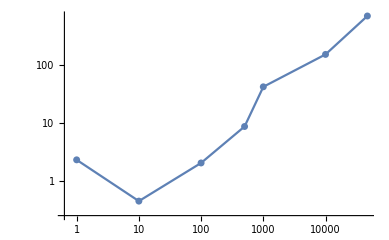

```mathematica
ListLogLogPlot[infoObjectsVSTime,PlotRange->All,Joined->True,Mesh->All]
```